```mathematica
pydata[f_]:=Table[((base+offset*Sin[(f*x/120)])/256)/.{base->9000,offset->7000},{x,0,3000-1}]
```

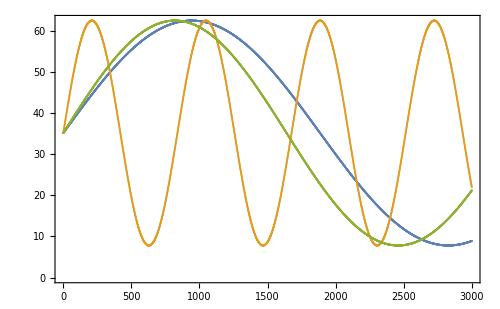

```mathematica
ListPlot[{pydata[0.2],pydata[0.9],pydata[0.23]}]
```

```mathematica
(First[#]-Last[#])&[pydata[0.2]]
(First[#]-Last[#])&[pydata[0.9]]
(First[#]-Last[#])&[pydata[0.23]]
(First[#]-Last[#])&[pydata[0.7]]
(First[#]-Last[#])&[pydata[0.45]]
```

26.2335

13.1417

13.9434

26.7118

26.4891

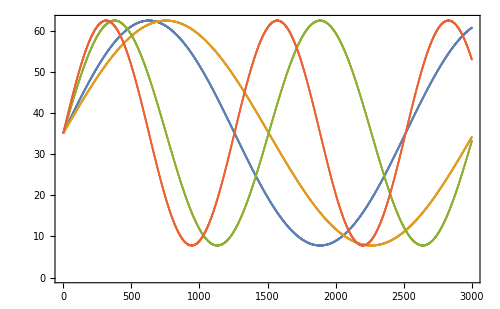

```mathematica
ListPlot[{pydata[0.3],pydata[0.25],pydata[0.5],pydata[0.6]}]
```

```mathematica
(First[#]-Last[#])&[pydata[0.3]]
(First[#]-Last[#])&[pydata[0.25]]
(First[#]-Last[#])&[pydata[0.5]]
(First[#]-Last[#])&[pydata[0.6]]
```

-25.6247

0.964177

1.92715

-17.8849

```mathematica
(First[#]-Last[#])&[pydata[0.45]]
```

26.4891

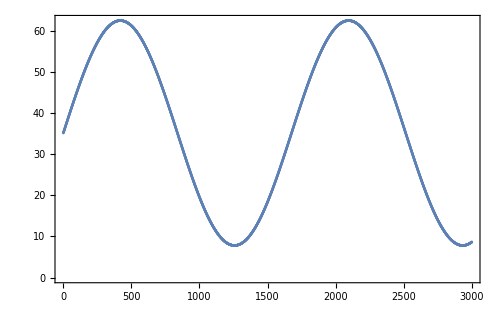

```mathematica
ListPlot[{pydata[0.45]}]
```

```mathematica
(First[#]-Last[#])&@Table[((base+offset*Sin[(0.45*x/120)])/256)/.{base->2000,offset->7000},{x,0,3000-1}]
```

26.4891

```mathematica
35.15625-35.20019520950325
```

-0.0439452

```mathematica
Table[((base+offset*Sin[(0.45*x/120)])/256)/.{base->9000,offset->3000},{x,0,3000-1}]//Length
```

3000

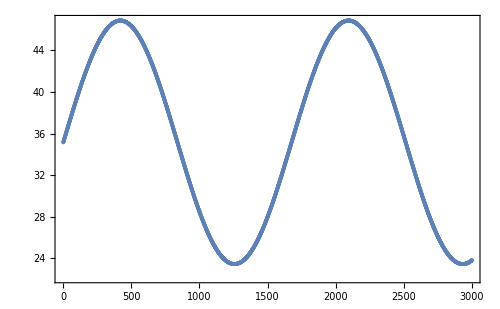

```mathematica
ListLinePlot[Table[((base+offset*Sin[(0.45*x/120)])/256)/.{base->9000,offset->3000},{x,0,3000-1}],Mesh->All]
```

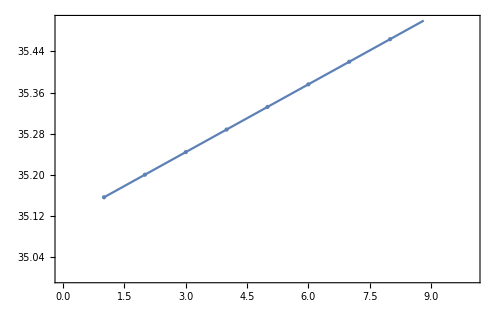

```mathematica
ListLinePlot[Table[((base+offset*Sin[(0.45*x/120)])/256)/.{base->9000,offset->3000},{x,0,3000-1}],PlotRange->{{0,10},{35,35.5}},Mesh->All,MeshStyle->{PointSize->Large}]
```

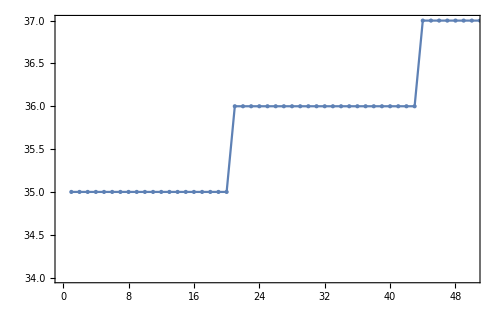

```mathematica
ListLinePlot[Table[((base+offset*Sin[(0.45*x/120)])/256)/.{base->9000,offset->3000}//Floor,{x,0,3000-1}],PlotRange->{{0,50},{34,37}},Mesh->All,MeshStyle->{PointSize->Large}]
```

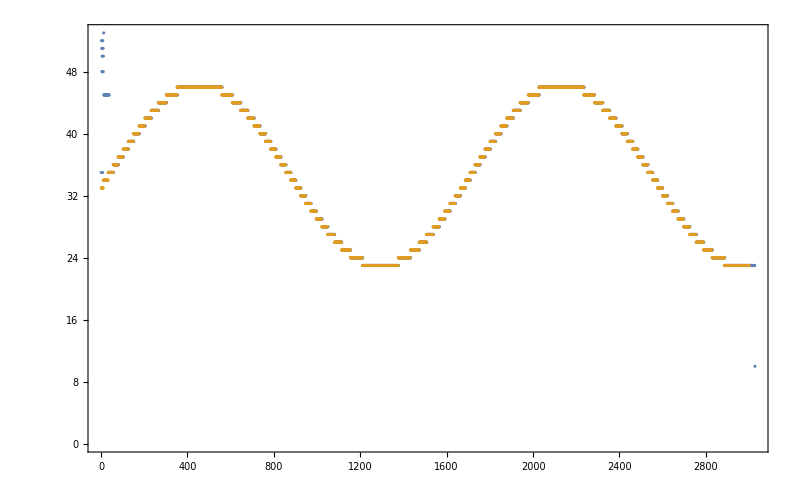

```mathematica
ListPlot[{{35,52,51,48,50,48,35,52,51,48,50,53,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,10},Table[((base+offset*Sin[(0.45*(x-35)/120)])/256)/.{base->9000,offset->3000}//Floor,{x,0,3000-1}]},ImageSize->800]
```

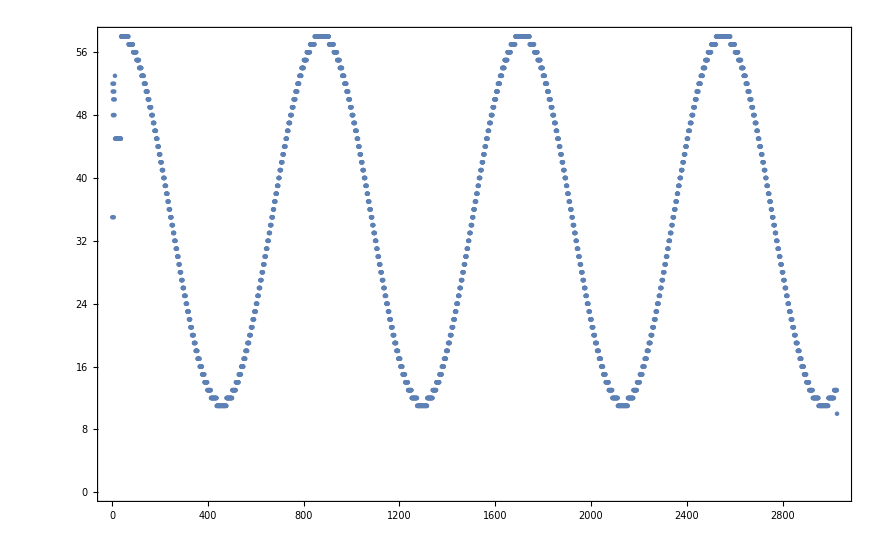

```mathematica
{35,52,51,48,50,48,35,52,51,48,50,53,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,50,50,50,50,50,50,50,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,47,47,47,47,47,47,46,46,46,46,46,46,46,45,45,45,45,45,45,44,44,44,44,44,44,43,43,43,43,43,43,42,42,42,42,42,42,41,41,41,41,41,41,40,40,40,40,40,40,39,39,39,39,39,39,38,38,38,38,38,38,37,37,37,37,37,36,36,36,36,36,36,35,35,35,35,35,35,34,34,34,34,34,34,33,33,33,33,33,32,32,32,32,32,32,31,31,31,31,31,31,30,30,30,30,30,30,29,29,29,29,29,28,28,28,28,28,28,27,27,27,27,27,27,26,26,26,26,26,26,25,25,25,25,25,25,25,24,24,24,24,24,24,23,23,23,23,23,23,23,22,22,22,22,22,22,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,21,21,21,21,21,21,21,22,22,22,22,22,22,22,23,23,23,23,23,23,23,24,24,24,24,24,24,25,25,25,25,25,25,26,26,26,26,26,26,27,27,27,27,27,27,28,28,28,28,28,28,29,29,29,29,29,29,30,30,30,30,30,30,31,31,31,31,31,31,32,32,32,32,32,32,33,33,33,33,33,34,34,34,34,34,34,35,35,35,35,35,35,36,36,36,36,36,37,37,37,37,37,37,38,38,38,38,38,38,39,39,39,39,39,39,40,40,40,40,40,41,41,41,41,41,41,42,42,42,42,42,42,43,43,43,43,43,43,44,44,44,44,44,44,44,45,45,45,45,45,45,46,46,46,46,46,46,47,47,47,47,47,47,47,48,48,48,48,48,48,48,49,49,49,49,49,49,49,50,50,50,50,50,50,50,50,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,50,50,50,50,50,50,50,49,49,49,49,49,49,49,48,48,48,48,48,48,48,47,47,47,47,47,47,47,46,46,46,46,46,46,46,45,45,45,45,45,45,44,44,44,44,44,44,43,43,43,43,43,43,42,42,42,42,42,42,41,41,41,41,41,41,40,40,40,40,40,40,39,39,39,39,39,39,38,38,38,38,38,37,37,37,37,37,37,36,36,36,36,36,36,35,35,35,35,35,35,34,34,34,34,34,33,33,33,33,33,33,32,32,32,32,32,32,31,31,31,31,31,30,30,30,30,30,30,29,29,29,29,29,29,28,28,28,28,28,28,27,27,27,27,27,27,26,26,26,26,26,26,25,25,25,25,25,25,24,24,24,24,24,24,24,23,23,23,23,23,23,22,22,22,22,22,22,22,21,21,21,21,21,21,21,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,21,21,21,21,21,21,21,22,22,22,22,22,22,22,23,23,23,23,23,23,24,24,24,24,24,24,24,25,25,25,25,25,25,26,26,26,26,26,26,27,27,27,27,27,27,28,28,28,28,28,28,29,29,29,29,29,29,30,30,30,30,30,30,31,31,31,31,31,31,32,32,32,32,32,33,33,33,33,33,33,34,34,34,34,34,34,35,35,35,35,35,36,36,36,36,36,36,37,37,37,37,37,37,38,38,38,38,38,38,39,39,39,39,39,40,40,40,40,40,40,41,41,41,41,41,41,42,42,42,42,42,42,43,43,43,43,43,43,44,44,44,44,44,44,45,45,45,45,45,45,45,46,46,46,46,46,46,47,47,47,47,47,47,47,48,48,48,48,48,48,48,49,49,49,49,49,49,49,50,50,50,50,50,50,50,50,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,50,50,50,50,50,50,50,50,49,49,49,49,49,49,49,48,48,48,48,48,48,48,47,47,47,47,47,47,47,46,46,46,46,46,46,45,45,45,45,45,45,45,44,44,44,44,44,44,43,43,43,43,43,43,42,42,42,42,42,42,41,41,41,41,41,41,40,40,40,40,40,40,39,39,39,39,39,38,38,38,38,38,38,37,37,37,37,37,37,36,36,36,36,36,36,35,35,35,35,35,34,34,34,34,34,34,33,33,33,33,33,33,32,32,32,32,32,31,31,31,31,31,31,30,30,30,30,30,30,29,29,29,29,29,29,28,28,28,28,28,28,27,27,27,27,27,27,26,26,26,26,26,26,25,25,25,25,25,25,24,24,24,24,24,24,24,23,23,23,23,23,23,22,22,22,22,22,22,22,21,21,21,21,21,21,21,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,21,21,21,21,21,21,21,22,22,22,22,22,22,22,23,23,23,23,23,23,24,24,24,24,24,24,24,25,25,25,25,25,25,26,26,26,26,26,26,27,27,27,27,27,27,28,28,28,28,28,28,29,29,29,29,29,29,30,30,30,30,30,30,31,31,31,31,31,32,32,32,32,32,32,33,33,33,33,33,33,34,34,34,34,34,35,35,35,35,35,35,36,36,36,36,36,36,37,37,37,37,37,37,38,38,38,38,38,39,39,39,39,39,39,40,40,40,40,40,40,41,41,41,41,41,41,42,42,42,42,42,42,43,43,43,43,43,43,44,44,44,44,44,44,45,45,45,45,45,45,46,46,46,46,46,46,46,47,47,47,47,47,47,47,48,48,48,48,48,48,48,49,49,49,49,49,49,49,50,50,50,50,50,50,50,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,50,50,50,50,50,50,50,50,49,49,49,49,49,49,49,48,48,48,48,48,48,48,47,47,47,47,47,47,47,46,46,46,46,46,46,45,45,45,45,45,45,44,44,44,44,44,44,44,43,43,43,43,43,43,42,42,42,42,42,42,41,41,41,41,41,41,40,40,40,40,40,39,39,39,39,39,39,38,38,38,38,38,38,37,37,37,37,37,37,36,36,36,36,36,35,35,35,35,35,35,34,34,34,34,34,34,33,33,33,33,33,32,32,32,32,32,32,31,31,31,31,31,31,30,30,30,30,30,30,29,29,29,29,29,29,28,28,28,28,28,28,27,27,27,27,27,27,26,26,26,26,26,26,25,25,25,25,25,25,24,24,24,24,24,24,23,23,23,23,23,23,23,22,22,22,22,22,22,22,21,21,21,21,21,21,21,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,10}//ListPlot
```

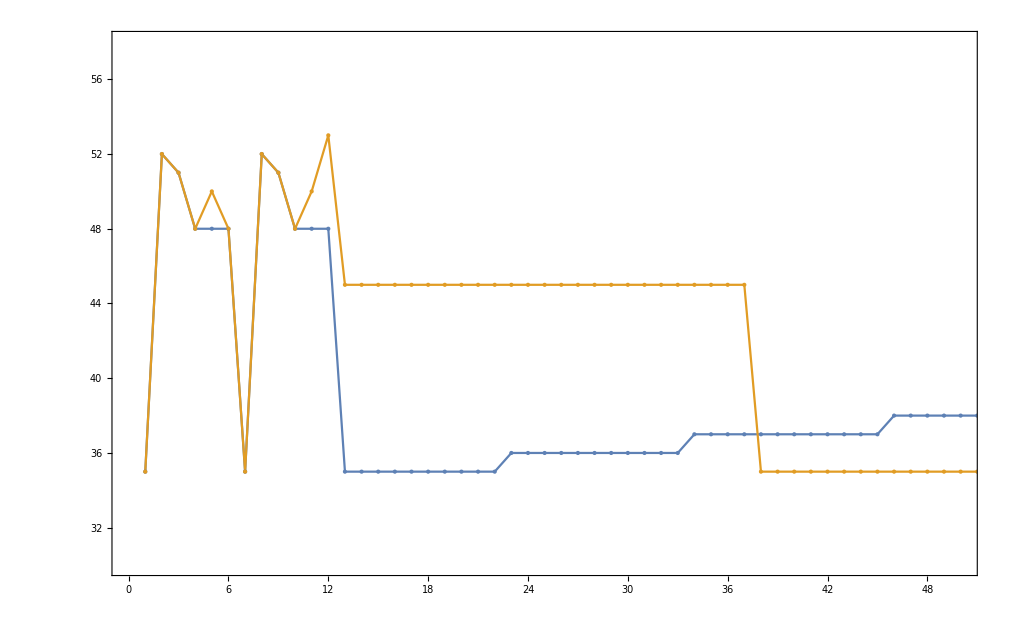

```mathematica
ListPlot[{{35,52,51,48,48,48,35,52,51,48,48,48,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,43,44,44,44,44,44,44,44,44,44,44,44,44,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,49,49,49,49,49,49,49,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,44,44,44,44,44,44,44,44,44,44,44,44,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,43,44,44,44,44,44,44,44,44,44,44,44,44,44,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,49,49,49,49,49,49,49,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,44,44,44,44,44,44,44,44,44,44,44,44,44,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,10},{35,52,51,48,50,48,35,52,51,48,50,53,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,10}},PlotRange->{{0,50},{30,All}},Joined->True,Mesh->All,MeshStyle->(PointSize->Medium)]
```

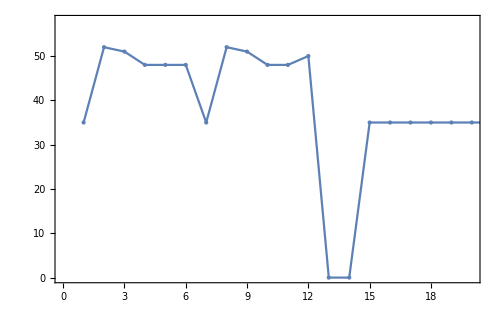

```mathematica
ListPlot[{35,52,51,48,48,48,35,52,51,48,48,50,0,0,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,10},PlotRange->{{0,20},All},Joined->True,Mesh->All,MeshStyle->(PointSize->Medium)]
```

```mathematica
Table[((base+offset*Sin[(0.23*(x-35)/120)])/256)/.{base->9000,offset->6000}//Floor,{x,0,3000-1}][[16]]
```

34

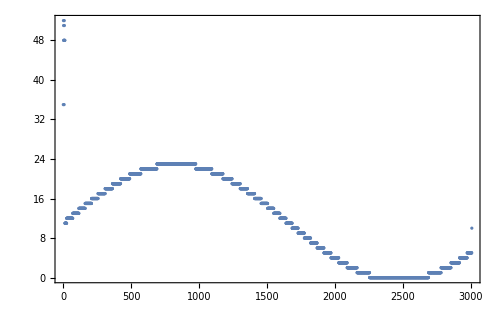

```mathematica
ListPlot[{35,52,51,48,48,48,35,52,51,48,48,48,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,10}]
```

```mathematica
PyListToExpression2[tuple_String]:=(StringToExpression2/@StringSplit[tuple,{"[",",","]"}])/;(Length[StringCases[tuple,"["~~__~~"]"]]===1)
```

```mathematica
StringToExpression2[string_String]:=Module[{expression,eReplaced},
eReplaced=StringReplace[string,{"e"->"*10^","E"->"*10^"}];
Return[
If[SyntaxQ[string],
expression=ToExpression[string];
If[NumericQ[expression],expression,
If[SyntaxQ[eReplaced],
expression=ToExpression[eReplaced];
If[NumericQ[expression],expression,string],string]],
string]
]
]
```

```mathematica
StringToExpression2["3 e-4"]
```

3/10000

```mathematica
PyListToExpression2["[-2.126719157834257e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29]"]
```

{-2.12672×10^38,-2.00018×10^-30,2.19478×10^-21,-2.37883×10^-12,0.0104342,-1.13058×10^7,1.23198×10^16,-1.34216×10^25,5.84757×10^34,5.52955×10^-34,-5.9878×10^-25,2.62113×10^-15,-2.83764×10^-6,-2.84602×10^-6,2.615×10^-15,-6.00585×10^-25,5.51639×10^-34,5.8657×10^34,-1.33883×10^25,1.23591×10^16,-1.12771×10^7,0.0104072,-2.38677×10^-12,2.18899×10^-21,-2.00707×10^-30,-2.11711×10^38,1.95247×10^29,-1.77735×10^20,1.63851×10^11,-37.2599,3.4338×10^-8,-3.14241×10^-17,2.87493×10^-26,-6.57341×10^-36,-6.90831×10^32,6.36007×10^23,-1.44169×10^14,132672.,132096.,-1.44655×10^14,6.33369×10^23,-6.93049×10^32,-6.54714×10^-36,2.88384×10^-26,-3.1303×10^-17,3.44399×10^-8,-37.3702,1.63251×10^11,-1.78239×10^20,1.94555×10^29,-2.12303×10^38,-2.00018×10^-30,2.19478×10^-21,-2.37883×10^-12,0.0104342,-1.13058×10^7,1.23198×10^16,-1.34216×10^25,5.84757×10^34,5.52955×10^-34,-5.9878×10^-25,2.62113×10^-15,-2.83764×10^-6,-2.84602×10^-6,2.615×10^-15,-6.00585×10^-25,5.51639×10^-34,5.8657×10^34,-1.33883×10^25,1.23591×10^16,-1.12771×10^7,0.0104072,-2.38677×10^-12,2.18899×10^-21,-2.00707×10^-30,-2.11711×10^38,1.95247×10^29,-1.77735×10^20,1.63851×10^11,-37.2599,3.4338×10^-8,-3.14241×10^-17,2.87493×10^-26,-6.57341×10^-36,-6.90831×10^32,6.36007×10^23,-1.44169×10^14,132672.,132096.,-1.44655×10^14,6.33369×10^23,-6.93049×10^32,-6.54714×10^-36,2.88384×10^-26,-3.1303×10^-17,3.44399×10^-8,-37.3702,1.63251×10^11,-1.78239×10^20,1.94555×10^29,-2.12303×10^38,-2.00018×10^-30,2.19478×10^-21,-2.37883×10^-12,0.0104342,-1.13058×10^7,1.23198×10^16,-1.34216×10^25,5.84757×10^34,5.52955×10^-34,-5.9878×10^-25,2.62113×10^-15,-2.83764×10^-6,-2.84602×10^-6,2.615×10^-15,-6.00585×10^-25,5.51639×10^-34,5.8657×10^34,-1.33883×10^25,1.23591×10^16,-1.12771×10^7,0.0104072,-2.38677×10^-12,2.18899×10^-21,-2.00707×10^-30,-2.11711×10^38,1.95247×10^29,-1.77735×10^20,1.63851×10^11,-37.2599,3.4338×10^-8,-3.14241×10^-17,2.87493×10^-26,-6.57341×10^-36,-6.90831×10^32,6.36007×10^23,-1.44169×10^14,132672.,132096.,-1.44655×10^14,6.33369×10^23,-6.93049×10^32,-6.54714×10^-36,2.88384×10^-26,-3.1303×10^-17,3.44399×10^-8,-37.3702,1.63251×10^11,-1.78239×10^20,1.94555×10^29,-2.12303×10^38,-2.00018×10^-30,2.19478×10^-21,-2.37883×10^-12,0.0104342,-1.13058×10^7,1.23198×10^16,-1.34216×10^25,5.84757×10^34,5.52955×10^-34,-5.9878×10^-25,2.62113×10^-15,-2.83764×10^-6,-2.84602×10^-6,2.615×10^-15,-6.00585×10^-25,5.51639×10^-34,5.8657×10^34,-1.33883×10^25,1.23591×10^16,-1.12771×10^7,0.0104072,-2.38677×10^-12,2.18899×10^-21,-2.00707×10^-30,-2.11711×10^38,1.95247×10^29,-1.77735×10^20,1.63851×10^11,-37.2599,3.4338×10^-8,-3.14241×10^-17,2.87493×10^-26,-6.57341×10^-36,-6.90831×10^32,6.36007×10^23,-1.44169×10^14,132672.,132096.,-1.44655×10^14,6.33369×10^23,-6.93049×10^32,-6.54714×10^-36,2.88384×10^-26,-3.1303×10^-17,3.44399×10^-8,-37.3702,1.63251×10^11,-1.78239×10^20,1.94555×10^29,-2.12303×10^38,-2.00018×10^-30,2.19478×10^-21,-2.37883×10^-12,0.0104342,-1.13058×10^7,1.23198×10^16,-1.34216×10^25,5.84757×10^34,5.52955×10^-34,-5.9878×10^-25,2.62113×10^-15,-2.83764×10^-6,-2.84602×10^-6,2.615×10^-15,-6.00585×10^-25,5.51639×10^-34,5.8657×10^34,-1.33883×10^25,1.23591×10^16,-1.12771×10^7,0.0104072,-2.38677×10^-12,2.18899×10^-21,-2.00707×10^-30,-2.11711×10^38,1.95247×10^29,-1.77735×10^20,1.63851×10^11,-37.2599,3.4338×10^-8,-3.14241×10^-17,2.87493×10^-26,-6.57341×10^-36,-6.90831×10^32,6.36007×10^23,-1.44169×10^14,132672.,132096.,-1.44655×10^14,6.33369×10^23,-6.93049×10^32,-6.54714×10^-36,2.88384×10^-26,-3.1303×10^-17,3.44399×10^-8,-37.3702,1.63251×10^11,-1.78239×10^20,1.94555×10^29,-2.12303×10^38,-2.00018×10^-30,2.19478×10^-21,-2.37883×10^-12,0.0104342,-1.13058×10^7,1.23198×10^16,-1.34216×10^25,5.84757×10^34,5.52955×10^-34,-5.9878×10^-25,2.62113×10^-15,-2.83764×10^-6,-2.84602×10^-6,2.615×10^-15,-6.00585×10^-25,5.51639×10^-34,5.8657×10^34,-1.33883×10^25,1.23591×10^16,-1.12771×10^7,0.0104072,-2.38677×10^-12,2.18899×10^-21,-2.00707×10^-30,-2.11711×10^38,1.95247×10^29,-1.77735×10^20,1.63851×10^11,-37.2599,3.4338×10^-8,-3.14241×10^-17,2.87493×10^-26,-6.57341×10^-36,-6.90831×10^32,6.36007×10^23,-1.44169×10^14,132672.,132096.,-1.44655×10^14,6.33369×10^23,-6.93049×10^32,-6.54714×10^-36,2.88384×10^-26,-3.1303×10^-17,3.44399×10^-8,-37.3702,1.63251×10^11,-1.78239×10^20,1.94555×10^29,-2.12303×10^38,-2.00018×10^-30,2.19478×10^-21,-2.37883×10^-12,0.0104342,-1.13058×10^7,1.23198×10^16,-1.34216×10^25,5.84757×10^34,5.52955×10^-34,-5.9878×10^-25,2.62113×10^-15,-2.83764×10^-6,-2.84602×10^-6,2.615×10^-15,-6.00585×10^-25,5.51639×10^-34,5.8657×10^34,-1.33883×10^25,1.23591×10^16,-1.12771×10^7,0.0104072,-2.38677×10^-12,2.18899×10^-21,-2.00707×10^-30,-2.11711×10^38,1.95247×10^29,-1.77735×10^20,1.63851×10^11,-37.2599,3.4338×10^-8,-3.14241×10^-17,2.87493×10^-26,-6.57341×10^-36,-6.90831×10^32,6.36007×10^23,-1.44169×10^14,132672.,132096.,-1.44655×10^14,6.33369×10^23,-6.93049×10^32,-6.54714×10^-36,2.88384×10^-26,-3.1303×10^-17,3.44399×10^-8,-37.3702,1.63251×10^11,-1.78239×10^20,1.94555×10^29,-2.12303×10^38,-2.00018×10^-30,2.19478×10^-21,-2.37883×10^-12,0.0104342,-1.13058×10^7,1.23198×10^16,-1.34216×10^25,5.84757×10^34,5.52955×10^-34,-5.9878×10^-25,2.62113×10^-15,-2.83764×10^-6,-2.84602×10^-6,2.615×10^-15,-6.00585×10^-25,5.51639×10^-34,5.8657×10^34,-1.33883×10^25,1.23591×10^16,-1.12771×10^7,0.0104072,-2.38677×10^-12,2.18899×10^-21,-2.00707×10^-30,-2.11711×10^38,1.95247×10^29,-1.77735×10^20,1.63851×10^11,-37.2599,3.4338×10^-8,-3.14241×10^-17,2.87493×10^-26,-6.57341×10^-36,-6.90831×10^32,6.36007×10^23,-1.44169×10^14,132672.,132096.,-1.44655×10^14,6.33369×10^23,-6.93049×10^32,-6.54714×10^-36,2.88384×10^-26,-3.1303×10^-17,3.44399×10^-8,-37.3702,1.63251×10^11,-1.78239×10^20,1.94555×10^29,-2.12303×10^38,-2.00018×10^-30,2.19478×10^-21,-2.37883×10^-12,0.0104342,-1.13058×10^7,1.23198×10^16,-1.34216×10^25,5.84757×10^34,5.52955×10^-34,-5.9878×10^-25,2.62113×10^-15,-2.83764×10^-6,-2.84602×10^-6,2.615×10^-15,-6.00585×10^-25,5.51639×10^-34,5.8657×10^34,-1.33883×10^25,1.23591×10^16,-1.12771×10^7,0.0104072,-2.38677×10^-12,2.18899×10^-21,-2.00707×10^-30,-2.11711×10^38,1.95247×10^29,-1.77735×10^20,1.63851×10^11,-37.2599,3.4338×10^-8,-3.14241×10^-17,2.87493×10^-26,-6.57341×10^-36,-6.90831×10^32,6.36007×10^23,-1.44169×10^14,132672.,132096.,-1.44655×10^14,6.33369×10^23,-6.93049×10^32,-6.54714×10^-36,2.88384×10^-26,-3.1303×10^-17,3.44399×10^-8,-37.3702,1.63251×10^11,-1.78239×10^20,1.94555×10^29,-2.12303×10^38,-2.00018×10^-30,2.19478×10^-21,-2.37883×10^-12,0.0104342,-1.13058×10^7,1.23198×10^16,-1.34216×10^25,5.84757×10^34,5.52955×10^-34,-5.9878×10^-25,2.62113×10^-15,-2.83764×10^-6,-2.84602×10^-6,2.615×10^-15,-6.00585×10^-25,5.51639×10^-34,5.8657×10^34,-1.33883×10^25,1.23591×10^16,-1.12771×10^7,0.0104072,-2.38677×10^-12,2.18899×10^-21,-2.00707×10^-30,-2.11711×10^38,1.95247×10^29,-1.77735×10^20,1.63851×10^11,-37.2599,3.4338×10^-8,-3.14241×10^-17,2.87493×10^-26,-6.57341×10^-36,-6.90831×10^32,6.36007×10^23,-1.44169×10^14,132672.,132096.,-1.44655×10^14,6.33369×10^23,-6.93049×10^32,-6.54714×10^-36,2.88384×10^-26,-3.1303×10^-17,3.44399×10^-8,-37.3702,1.63251×10^11,-1.78239×10^20,1.94555×10^29}

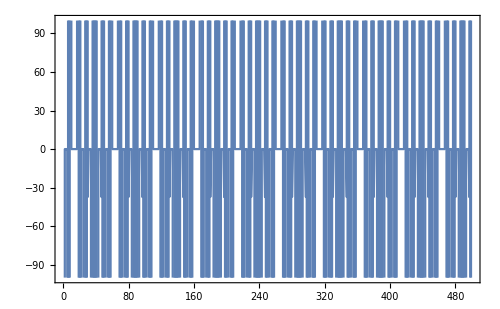

```mathematica
ListPlot[PyListToExpression2["[-2.126719157834257e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29, -2.1230324242406014e+38, -2.000180750353536e-30, 2.194775727238316e-21, -2.3788276036496026e-12, 0.010434187948703766, -11305771.0, 1.231980230344704e+16, -1.3421611180358112e+25, 5.847570707769601e+34, 5.529549762674522e-34, -5.987797425121251e-25, 2.6211252440700664e-15, -2.837637339325738e-06, -2.8460196972446283e-06, 2.6150001370702338e-15, -6.005847548708839e-25, 5.516385603477755e-34, 5.865699101704896e+34, -1.3388262925837358e+25, 1.235911199162368e+16, -11277102.0, 0.010407249443233013, -2.3867661319565414e-12, 2.18898606879562e-21, -2.0070663260629128e-30, -2.11711381429416e+38, 1.95246922255019e+29, -1.7773505187538587e+20, 163850895360.0, -37.25985336303711, 3.433804351971048e-08, -3.142413155846894e-17, 2.874929305219322e-26, -6.57340975357446e-36, -6.908307367556524e+32, 6.360073465765162e+23, -144169251110912.0, 132672.03125, 132096.0, -144654532083712.0, 6.333693180587876e+23, -6.930488931922945e+32, -6.547143366743647e-36, 2.883842509001946e-26, -3.1302999229566677e-17, 3.443989626816801e-08, -37.37019348144531, 163251077120.0, -1.7823940225709323e+20, 1.945553789072676e+29]"],PlotRange->{-100,100},Joined->True]
```

```mathematica
PyListToExpression2["[5.997589482831245e-07, -2.174128434809876e-18, 3.1918918450815757e-29, 1.3398114838811613e+37, -4.887074232523585e+25, 178263188045824.0, -650.2208251953125, 9.544949719497708e-09, -3.4602732475417626e-20, 1.2698238933444184e-31, 5.330615365356293e+34, -1.94429331055245e+23, 2836634271744.0, -10.346226692199707, 3.7963538562779675e-11, -1.3763880991227928e-22, 2.0200705114987926e-33, 8.480414619909027e+32, -3.0930111440081104e+21, 11281145856.0, -0.04114452004432678, 6.037969603467364e-13, -2.1891791393467293e-24, 8.03122722606601e-36, 3.3718518757246605e+30, -1.2297406437000217e+19, 179397296.0, -0.0006542677874676883, 2.3999990346180956e-15, -8.702352972312613e-27, 1.2768340136847154e-37, 5.3608819051482845e+28, -1.955071346522194e+17, 713010.875, -2.6002630875154864e-06, 3.8147975046724634e-17, -1.3832855806759e-28, -5.841227990261502e+37, 2.1302211511948236e+26, -776842545987584.0, 11331.7978515625, -4.132397535272503e-08, 1.5154343025232137e-19, -5.49554423557447e-31, -2.320520386274102e+35, 3.384844663322297e+24, -12343252615168.0, 45.01191711425781, -1.6413964631922795e-10, 2.4074162765753882e-21, -8.730482501581533e-33, -3.6863443481692116e+33, 1.3442549081558502e+22, -49018003456.0, 0.7149690985679626, -2.607093143799921e-12, 9.558260768242072e-24, -3.4665489117867535e-35, -1.463654226932677e+31, 2.1348063229122078e+20, -778423872.0, 0.002838446293026209, -1.0349843066457566e-14, 1.517617758516136e-25, -5.50418691874421e-37, -2.323905069313709e+29, 8.473669483699896e+17, -3089679.0, 4.506226468947716e-05, -1.6430487030487801e-16, 6.022366084211873e-28, 2.529336143792025e+38, -9.222260804991776e+26, 1.3450118510411776e+16, -49040.24609375, -49150.24609375, 1.3480080202268672e+16, -9.194494027942265e+26, 2.5349957473678278e+38, 6.004370676294005e-28, -1.646741766698809e-16, 4.516377885011025e-05, -3080271.25, 8.49284496648831e+17, -2.3168451314218188e+29, -5.516699505095736e-37, 1.512979379652953e-25, -1.037347867381775e-14, 0.0028449431993067265, -776031872.0, 2.1397152465060417e+20, -1.4591049181808853e+31, -3.4745569670517303e-35, 9.528777091909437e-24, -2.6131438592841283e-12, 0.7166323065757751, -48863866880.0, 1.3473966192559038e+22, -3.674777345927139e+33, -8.750983123059874e-33, 2.399816756645949e-21, -1.645268921102172e-10, 45.11836242675781, -12304062087168.0, 3.392887443738434e+24, -2.3130667988151662e+35, -5.508664633320608e-31, 1.5106036969928747e-19, -4.142311027521828e-08, 11359.0478515625, -774317172326400.0, 2.1353685306611516e+26, -5.82227661378809e+37, -1.3866444024989113e-28, 3.80234645122007e-17, -2.6066077225550544e-06, 714754.875, -1.948650370414674e+17, 5.374059196582084e+28, 1.2726154326838348e-37, -8.723849431979886e-27, 2.3920845705171882e-15, -0.0006558920140378177, 179843760.0, -1.2256030714935378e+19, 3.380285342242292e+30, 8.004411978652691e-36, -2.194682233021551e-24, 6.017569797490963e-13, -0.041248470544815063, 11309719552.0, -3.0824910167535497e+21, 8.502004294194164e+32, 2.01315878838695e-33, -1.3799100790746787e-22, 3.783386798295041e-11, -10.372838020324707, 2843949137920.0, -1.937514312249347e+23, 5.344432756898781e+34, 1.26543048320822e-31, -3.4692895162185906e-20, 9.511526677385973e-09, -651.9239501953125, 178731339481088.0, -4.8698380560297125e+25, 1.3433487361160382e+37, 3.1805676779351325e-29, -2.1798988467630457e-18, 5.976198735879734e-07, -655345.9375, 1.796607325545431e+17, -1.2235877050114808e+28, -2.9152114389560195e-38, 7.991775726727098e-27, -2.190799260821702e-15, 0.0006005780887790024, -40897652.0, 1.1283236702748934e+19, -3.073271981259149e+30, -7.322430822211242e-36, 2.0072713644768374e-24, -1.375604545637149e-13, 0.037708379328250885, -10269517824.0, 2.833383692039782e+21, -1.9290125225193294e+32, -4.59654658027993e-34, 1.259967123206062e-22, -3.4536009468899564e-11, 9.466574668884277, -644414373888.0, 1.77813174129272e+23, -4.841422066263999e+34, -1.153694690536853e-31, 3.162235549194932e-20, -2.1668755678661e-09, 593.923095703125, -161688674369536.0, 4.461700615218676e+25, -3.0364449982838354e+36, -7.236502714735521e-30, 1.983384307867904e-18, -5.435877596937644e-07, 148984.265625, -1.0137790339612672e+16, 2.7977613004096384e+27, 1.489120641680982e-39, -1.8148267051624306e-27, 4.973785407211132e-16, -3.4078075259458274e-05, 9339406.0, -2.541511781755388e+18, 7.014294141991932e+29, 1.6601125958086518e-36, -1.137381132261852e-25, 3.116955207393274e-14, -0.008541594259440899, 2340752128.0, -1.5921144754084826e+20, 4.39456818116245e+31, 1.0400197748337208e-34, -2.849898544085862e-23, 7.809538606073918e-12, -0.5350041389465332, 146603638784.0, -3.987728503013864e+22, 1.1007652652662105e+34, 2.604897538537303e-32, -1.7844365881203694e-21, 4.889532112528627e-10, -133.9727325439453, 36709106450432.0, -2.4956983403721934e+24, 6.889937711486973e+35, 1.6303485984887894e-30, -4.466909207648006e-19, 1.2238892566074355e-07, -8383.251953125, 2296880327294976.0, -6.24467001802703e+26, 1.7241023747005856e+38, 4.079397437606643e-28, -2.7941075831077605e-17, 7.655005902051926e-06, 7.62939453125e-06, -2.7848749239826887e-17, 4.097516105040952e-28, 1.7184427711247826e+38, -6.272247900417226e+26, 2289389904330752.0, -8356.001953125, 1.2292369433453132e-07, -4.452483177765082e-19, 1.6373780547067066e-30, 6.867829885018993e+35, -2.5065447376571585e+24, 36592068591616.0, -133.5469512939453, 4.91027940530131e-10, -1.778801420197352e-21, 2.6159562955162514e-32, 1.0973109173805886e+34, -4.0045607066211614e+22, 146146459648.0, -0.5333409309387207, 7.84217829563616e-12, -2.841093594206147e-23, 1.044310214419852e-34, 4.381074634734239e+31, -1.5987345909388568e+20, 2333608704.0, -0.008515606634318829, 3.1296183499547256e-14, -1.1339416987150885e-25, 1.6668623254100607e-36, 6.993210475697853e+29, -2.55178534352742e+18, 9311502.0, -3.3976561098825186e-05, 4.993707092734961e-16, -1.8094525902456124e-27, 1.541494171785122e-39, 2.789525493263514e+27, -1.0178196318191616e+16, 148548.265625, -5.420016009338724e-07, 1.9911132767164465e-18, -7.2155100783417e-30, -3.0483707382181325e+36, 4.448832166552856e+25, -162315722817536.0, 592.219970703125, -2.160679635210272e-09, 3.1743947810820346e-20, -1.1504145911003186e-31, -4.859929269851316e+34, 1.7731050035326342e+23, -646880559104.0, 9.439963340759277, -3.443919802115225e-11, 1.2646845114192837e-22, -4.583733691855967e-34, -1.9362914165221963e+32, 2.825529414289648e+21, -10307789824.0, 0.037604428827762604, -1.3718228484595196e-13, 2.0146927706579304e-24, -7.3024106840488e-36, -3.0845678818861734e+30, 1.1252555930287473e+19, -41048176.0, 0.000598953862208873, -2.184890358981656e-15, 8.020568379395687e-27, -2.9073910724863155e-38, -1.2280303893394025e+28, 1.7918134548483277e+17, -653601.9375, 5.997589482831245e-07, -2.174128434809876e-18, 3.1918918450815757e-29, 1.3398114838811613e+37, -4.887074232523585e+25, 178263188045824.0, -650.2208251953125, 9.544949719497708e-09, -3.4602732475417626e-20, 1.2698238933444184e-31, 5.330615365356293e+34, -1.94429331055245e+23, 2836634271744.0, -10.346226692199707, 3.7963538562779675e-11, -1.3763880991227928e-22, 2.0200705114987926e-33, 8.480414619909027e+32, -3.0930111440081104e+21, 11281145856.0, -0.04114452004432678, 6.037969603467364e-13, -2.1891791393467293e-24, 8.03122722606601e-36, 3.3718518757246605e+30, -1.2297406437000217e+19, 179397296.0, -0.0006542677874676883, 2.3999990346180956e-15, -8.702352972312613e-27, 1.2768340136847154e-37, 5.3608819051482845e+28, -1.955071346522194e+17, 713010.875, -2.6002630875154864e-06, 3.8147975046724634e-17, -1.3832855806759e-28, -5.841227990261502e+37, 2.1302211511948236e+26, -776842545987584.0, 11331.7978515625, -4.132397535272503e-08, 1.5154343025232137e-19, -5.49554423557447e-31, -2.320520386274102e+35, 3.384844663322297e+24, -12343252615168.0, 45.01191711425781, -1.6413964631922795e-10, 2.4074162765753882e-21, -8.730482501581533e-33, -3.6863443481692116e+33, 1.3442549081558502e+22, -49018003456.0, 0.7149690985679626, -2.607093143799921e-12, 9.558260768242072e-24, -3.4665489117867535e-35, -1.463654226932677e+31, 2.1348063229122078e+20, -778423872.0, 0.002838446293026209, -1.0349843066457566e-14, 1.517617758516136e-25, -5.50418691874421e-37, -2.323905069313709e+29, 8.473669483699896e+17, -3089679.0, 4.506226468947716e-05, -1.6430487030487801e-16, 6.022366084211873e-28, 2.529336143792025e+38, -9.222260804991776e+26, 1.3450118510411776e+16, -49040.24609375, -49150.24609375, 1.3480080202268672e+16, -9.194494027942265e+26, 2.5349957473678278e+38, 6.004370676294005e-28, -1.646741766698809e-16, 4.516377885011025e-05, -3080271.25, 8.49284496648831e+17, -2.3168451314218188e+29, -5.516699505095736e-37, 1.512979379652953e-25, -1.037347867381775e-14, 0.0028449431993067265, -776031872.0, 2.1397152465060417e+20, -1.4591049181808853e+31, -3.4745569670517303e-35, 9.528777091909437e-24, -2.6131438592841283e-12, 0.7166323065757751, -48863866880.0, 1.3473966192559038e+22, -3.674777345927139e+33, -8.750983123059874e-33, 2.399816756645949e-21, -1.645268921102172e-10, 45.11836242675781, -12304062087168.0, 3.392887443738434e+24, -2.3130667988151662e+35, -5.508664633320608e-31, 1.5106036969928747e-19, -4.142311027521828e-08, 11359.0478515625, -774317172326400.0, 2.1353685306611516e+26, -5.82227661378809e+37, -1.3866444024989113e-28, 3.80234645122007e-17, -2.6066077225550544e-06, 714754.875, -1.948650370414674e+17, 5.374059196582084e+28, 1.2726154326838348e-37, -8.723849431979886e-27, 2.3920845705171882e-15, -0.0006558920140378177, 179843760.0, -1.2256030714935378e+19, 3.380285342242292e+30, 8.004411978652691e-36, -2.194682233021551e-24, 6.017569797490963e-13, -0.041248470544815063, 11309719552.0, -3.0824910167535497e+21, 8.502004294194164e+32, 2.01315878838695e-33, -1.3799100790746787e-22, 3.783386798295041e-11, -10.372838020324707, 2843949137920.0, -1.937514312249347e+23, 5.344432756898781e+34, 1.26543048320822e-31, -3.4692895162185906e-20, 9.511526677385973e-09, -651.9239501953125, 178731339481088.0, -4.8698380560297125e+25, 1.3433487361160382e+37, 3.1805676779351325e-29, -2.1798988467630457e-18, 5.976198735879734e-07, -655345.9375, 1.796607325545431e+17, -1.2235877050114808e+28, -2.9152114389560195e-38, 7.991775726727098e-27, -2.190799260821702e-15, 0.0006005780887790024, -40897652.0, 1.1283236702748934e+19, -3.073271981259149e+30, -7.322430822211242e-36, 2.0072713644768374e-24, -1.375604545637149e-13, 0.037708379328250885, -10269517824.0, 2.833383692039782e+21, -1.9290125225193294e+32, -4.59654658027993e-34, 1.259967123206062e-22, -3.4536009468899564e-11, 9.466574668884277, -644414373888.0, 1.77813174129272e+23, -4.841422066263999e+34, -1.153694690536853e-31, 3.162235549194932e-20, -2.1668755678661e-09, 593.923095703125, -161688674369536.0, 4.461700615218676e+25, -3.0364449982838354e+36, -7.236502714735521e-30, 1.983384307867904e-18, -5.435877596937644e-07, 148984.265625, -1.0137790339612672e+16, 2.7977613004096384e+27, 1.489120641680982e-39, -1.8148267051624306e-27, 4.973785407211132e-16, -3.4078075259458274e-05, 9339406.0, -2.541511781755388e+18, 7.014294141991932e+29, 1.6601125958086518e-36, -1.137381132261852e-25, 3.116955207393274e-14, -0.008541594259440899, 2340752128.0, -1.5921144754084826e+20, 4.39456818116245e+31, 1.0400197748337208e-34, -2.849898544085862e-23, 7.809538606073918e-12, -0.5350041389465332, 146603638784.0, -3.987728503013864e+22, 1.1007652652662105e+34, 2.604897538537303e-32, -1.7844365881203694e-21, 4.889532112528627e-10, -133.9727325439453, 36709106450432.0, -2.4956983403721934e+24, 6.889937711486973e+35, 1.6303485984887894e-30, -4.466909207648006e-19, 1.2238892566074355e-07, -8383.251953125, 2296880327294976.0, -6.24467001802703e+26, 1.7241023747005856e+38, 4.079397437606643e-28, -2.7941075831077605e-17, 7.655005902051926e-06, 7.62939453125e-06, -2.7848749239826887e-17, 4.097516105040952e-28, 1.7184427711247826e+38, -6.272247900417226e+26, 2289389904330752.0, -8356.001953125, 1.2292369433453132e-07, -4.452483177765082e-19, 1.6373780547067066e-30, 6.867829885018993e+35, -2.5065447376571585e+24, 36592068591616.0, -133.5469512939453, 4.91027940530131e-10, -1.778801420197352e-21, 2.6159562955162514e-32, 1.0973109173805886e+34, -4.0045607066211614e+22, 146146459648.0, -0.5333409309387207, 7.84217829563616e-12, -2.841093594206147e-23, 1.044310214419852e-34, 4.381074634734239e+31, -1.5987345909388568e+20, 2333608704.0, -0.008515606634318829, 3.1296183499547256e-14, -1.1339416987150885e-25, 1.6668623254100607e-36, 6.993210475697853e+29, -2.55178534352742e+18, 9311502.0, -3.3976561098825186e-05, 4.993707092734961e-16, -1.8094525902456124e-27, 1.541494171785122e-39, 2.789525493263514e+27, -1.0178196318191616e+16, 148548.265625, -5.420016009338724e-07, 1.9911132767164465e-18, -7.2155100783417e-30, -3.0483707382181325e+36, 4.448832166552856e+25, -162315722817536.0, 592.219970703125, -2.160679635210272e-09, 3.1743947810820346e-20, -1.1504145911003186e-31, -4.859929269851316e+34, 1.7731050035326342e+23, -646880559104.0, 9.439963340759277, -3.443919802115225e-11, 1.2646845114192837e-22, -4.583733691855967e-34, -1.9362914165221963e+32, 2.825529414289648e+21, -10307789824.0, 0.037604428827762604, -1.3718228484595196e-13, 2.0146927706579304e-24, -7.3024106840488e-36, -3.0845678818861734e+30, 1.1252555930287473e+19, -41048176.0, 0.000598953862208873, -2.184890358981656e-15, 8.020568379395687e-27, -2.9073910724863155e-38, -1.2280303893394025e+28, 1.7918134548483277e+17, -653601.9375, 5.997589482831245e-07, -2.174128434809876e-18, 3.1918918450815757e-29, 1.3398114838811613e+37, -4.887074232523585e+25, 178263188045824.0, -650.2208251953125, 9.544949719497708e-09, -3.4602732475417626e-20, 1.2698238933444184e-31, 5.330615365356293e+34, -1.94429331055245e+23, 2836634271744.0, -10.346226692199707, 3.7963538562779675e-11, -1.3763880991227928e-22, 2.0200705114987926e-33, 8.480414619909027e+32, -3.0930111440081104e+21, 11281145856.0, -0.04114452004432678, 6.037969603467364e-13, -2.1891791393467293e-24, 8.03122722606601e-36, 3.3718518757246605e+30, -1.2297406437000217e+19, 179397296.0, -0.0006542677874676883, 2.3999990346180956e-15, -8.702352972312613e-27, 1.2768340136847154e-37, 5.3608819051482845e+28, -1.955071346522194e+17, 713010.875, -2.6002630875154864e-06, 3.8147975046724634e-17, -1.3832855806759e-28, -5.841227990261502e+37, 2.1302211511948236e+26, -776842545987584.0, 11331.7978515625, -4.132397535272503e-08, 1.5154343025232137e-19, -5.49554423557447e-31, -2.320520386274102e+35, 3.384844663322297e+24, -12343252615168.0, 45.01191711425781, -1.6413964631922795e-10, 2.4074162765753882e-21, -8.730482501581533e-33, -3.6863443481692116e+33, 1.3442549081558502e+22, -49018003456.0, 0.7149690985679626, -2.607093143799921e-12, 9.558260768242072e-24, -3.4665489117867535e-35, -1.463654226932677e+31, 2.1348063229122078e+20, -778423872.0, 0.002838446293026209, -1.0349843066457566e-14, 1.517617758516136e-25, -5.50418691874421e-37, -2.323905069313709e+29, 8.473669483699896e+17, -3089679.0, 4.506226468947716e-05, -1.6430487030487801e-16, 6.022366084211873e-28, 2.529336143792025e+38, -9.222260804991776e+26, 1.3450118510411776e+16, -49040.24609375, -49150.24609375, 1.3480080202268672e+16, -9.194494027942265e+26, 2.5349957473678278e+38, 6.004370676294005e-28, -1.646741766698809e-16, 4.516377885011025e-05, -3080271.25, 8.49284496648831e+17, -2.3168451314218188e+29, -5.516699505095736e-37, 1.512979379652953e-25, -1.037347867381775e-14, 0.0028449431993067265, -776031872.0, 2.1397152465060417e+20, -1.4591049181808853e+31, -3.4745569670517303e-35, 9.528777091909437e-24, -2.6131438592841283e-12, 0.7166323065757751, -48863866880.0, 1.3473966192559038e+22, -3.674777345927139e+33, -8.750983123059874e-33, 2.399816756645949e-21, -1.645268921102172e-10, 45.11836242675781, -12304062087168.0, 3.392887443738434e+24, -2.3130667988151662e+35, -5.508664633320608e-31, 1.5106036969928747e-19, -4.142311027521828e-08, 11359.0478515625, -774317172326400.0, 2.1353685306611516e+26, -5.82227661378809e+37, -1.3866444024989113e-28, 3.80234645122007e-17, -2.6066077225550544e-06, 714754.875, -1.948650370414674e+17, 5.374059196582084e+28, 1.2726154326838348e-37, -8.723849431979886e-27, 2.3920845705171882e-15, -0.0006558920140378177, 179843760.0, -1.2256030714935378e+19, 3.380285342242292e+30, 8.004411978652691e-36, -2.194682233021551e-24, 6.017569797490963e-13, -0.041248470544815063, 11309719552.0, -3.0824910167535497e+21, 8.502004294194164e+32, 2.01315878838695e-33, -1.3799100790746787e-22, 3.783386798295041e-11, -10.372838020324707, 2843949137920.0, -1.937514312249347e+23, 5.344432756898781e+34, 1.26543048320822e-31, -3.4692895162185906e-20, 9.511526677385973e-09, -651.9239501953125, 178731339481088.0, -4.8698380560297125e+25, 1.3433487361160382e+37, 3.1805676779351325e-29, -2.1798988467630457e-18, 5.976198735879734e-07, -655345.9375, 1.796607325545431e+17, -1.2235877050114808e+28, -2.9152114389560195e-38, 7.991775726727098e-27, -2.190799260821702e-15, 0.0006005780887790024, -40897652.0, 1.1283236702748934e+19, -3.073271981259149e+30, -7.322430822211242e-36, 2.0072713644768374e-24, -1.375604545637149e-13, 0.037708379328250885, -10269517824.0, 2.833383692039782e+21, -1.9290125225193294e+32, -4.59654658027993e-34, 1.259967123206062e-22, -3.4536009468899564e-11, 9.466574668884277, -644414373888.0, 1.77813174129272e+23, -4.841422066263999e+34, -1.153694690536853e-31, 3.162235549194932e-20, -2.1668755678661e-09, 593.923095703125, -161688674369536.0, 4.461700615218676e+25, -3.0364449982838354e+36, -7.236502714735521e-30, 1.983384307867904e-18, -5.435877596937644e-07, 148984.265625, -1.0137790339612672e+16, 2.7977613004096384e+27, 1.489120641680982e-39, -1.8148267051624306e-27, 4.973785407211132e-16, -3.4078075259458274e-05, 9339406.0, -2.541511781755388e+18, 7.014294141991932e+29, 1.6601125958086518e-36, -1.137381132261852e-25, 3.116955207393274e-14, -0.008541594259440899, 2340752128.0, -1.5921144754084826e+20, 4.39456818116245e+31, 1.0400197748337208e-34, -2.849898544085862e-23, 7.809538606073918e-12, -0.5350041389465332, 146603638784.0, -3.987728503013864e+22, 1.1007652652662105e+34, 2.604897538537303e-32, -1.7844365881203694e-21, 4.889532112528627e-10, -133.9727325439453, 36709106450432.0, -2.4956983403721934e+24, 6.889937711486973e+35, 1.6303485984887894e-30, -4.466909207648006e-19, 1.2238892566074355e-07, -8383.251953125, 2296880327294976.0, -6.24467001802703e+26, 1.7241023747005856e+38, 4.079397437606643e-28, -2.7941075831077605e-17, 7.655005902051926e-06, 7.62939453125e-06, -2.7848749239826887e-17, 4.097516105040952e-28, 1.7184427711247826e+38, -6.272247900417226e+26, 2289389904330752.0, -8356.001953125, 1.2292369433453132e-07, -4.452483177765082e-19, 1.6373780547067066e-30, 6.867829885018993e+35, -2.5065447376571585e+24, 36592068591616.0, -133.5469512939453, 4.91027940530131e-10, -1.778801420197352e-21, 2.6159562955162514e-32, 1.0973109173805886e+34, -4.0045607066211614e+22, 146146459648.0, -0.5333409309387207, 7.84217829563616e-12, -2.841093594206147e-23, 1.044310214419852e-34, 4.381074634734239e+31, -1.5987345909388568e+20, 2333608704.0, -0.008515606634318829, 3.1296183499547256e-14, -1.1339416987150885e-25, 1.6668623254100607e-36, 6.993210475697853e+29, -2.55178534352742e+18, 9311502.0, -3.3976561098825186e-05, 4.993707092734961e-16, -1.8094525902456124e-27, 1.541494171785122e-39, 2.789525493263514e+27, -1.0178196318191616e+16, 148548.265625, -5.420016009338724e-07, 1.9911132767164465e-18, -7.2155100783417e-30, -3.0483707382181325e+36, 4.448832166552856e+25, -162315722817536.0, 592.219970703125, -2.160679635210272e-09, 3.1743947810820346e-20, -1.1504145911003186e-31, -4.859929269851316e+34, 1.7731050035326342e+23, -646880559104.0, 9.439963340759277, -3.443919802115225e-11, 1.2646845114192837e-22, -4.583733691855967e-34, -1.9362914165221963e+32, 2.825529414289648e+21, -10307789824.0, 0.037604428827762604, -1.3718228484595196e-13, 2.0146927706579304e-24, -7.3024106840488e-36, -3.0845678818861734e+30, 1.1252555930287473e+19, -41048176.0, 0.000598953862208873, -2.184890358981656e-15, 8.020568379395687e-27, -2.9073910724863155e-38, -1.2280303893394025e+28, 1.7918134548483277e+17, -653601.9375, 5.997589482831245e-07, -2.174128434809876e-18, 3.1918918450815757e-29, 1.3398114838811613e+37, -4.887074232523585e+25, 178263188045824.0, -650.2208251953125, 9.544949719497708e-09, -3.4602732475417626e-20, 1.2698238933444184e-31, 5.330615365356293e+34, -1.94429331055245e+23, 2836634271744.0, -10.346226692199707, 3.7963538562779675e-11, -1.3763880991227928e-22, 2.0200705114987926e-33, 8.480414619909027e+32, -3.0930111440081104e+21, 11281145856.0, -0.04114452004432678, 6.037969603467364e-13, -2.1891791393467293e-24, 8.03122722606601e-36, 3.3718518757246605e+30, -1.2297406437000217e+19, 179397296.0, -0.0006542677874676883, 2.3999990346180956e-15, -8.702352972312613e-27, 1.2768340136847154e-37, 5.3608819051482845e+28, -1.955071346522194e+17, 713010.875, -2.6002630875154864e-06, 3.8147975046724634e-17, -1.3832855806759e-28, -5.841227990261502e+37, 2.1302211511948236e+26, -776842545987584.0, 11331.7978515625, -4.132397535272503e-08, 1.5154343025232137e-19, -5.49554423557447e-31, -2.320520386274102e+35, 3.384844663322297e+24, -12343252615168.0, 45.01191711425781, -1.6413964631922795e-10, 2.4074162765753882e-21, -8.730482501581533e-33, -3.6863443481692116e+33, 1.3442549081558502e+22, -49018003456.0, 0.7149690985679626, -2.607093143799921e-12, 9.558260768242072e-24, -3.4665489117867535e-35, -1.463654226932677e+31, 2.1348063229122078e+20, -778423872.0, 0.002838446293026209, -1.0349843066457566e-14, 1.517617758516136e-25, -5.50418691874421e-37, -2.323905069313709e+29, 8.473669483699896e+17, -3089679.0, 4.506226468947716e-05, -1.6430487030487801e-16, 6.022366084211873e-28, 2.529336143792025e+38, -9.222260804991776e+26, 1.3450118510411776e+16, -49040.24609375, -49150.24609375, 1.3480080202268672e+16, -9.194494027942265e+26, 2.5349957473678278e+38, 6.004370676294005e-28, -1.646741766698809e-16, 4.516377885011025e-05, -3080271.25, 8.49284496648831e+17, -2.3168451314218188e+29, -5.516699505095736e-37, 1.512979379652953e-25, -1.037347867381775e-14, 0.0028449431993067265, -776031872.0, 2.1397152465060417e+20, -1.4591049181808853e+31, -3.4745569670517303e-35, 9.528777091909437e-24, -2.6131438592841283e-12, 0.7166323065757751, -48863866880.0, 1.3473966192559038e+22, -3.674777345927139e+33, -8.750983123059874e-33, 2.399816756645949e-21, -1.645268921102172e-10, 45.11836242675781, -12304062087168.0, 3.392887443738434e+24, -2.3130667988151662e+35, -5.508664633320608e-31, 1.5106036969928747e-19, -4.142311027521828e-08, 11359.0478515625, -774317172326400.0, 2.1353685306611516e+26, -5.82227661378809e+37, -1.3866444024989113e-28, 3.80234645122007e-17, -2.6066077225550544e-06, 714754.875, -1.948650370414674e+17, 5.374059196582084e+28, 1.2726154326838348e-37, -8.723849431979886e-27, 2.3920845705171882e-15, -0.0006558920140378177, 179843760.0, -1.2256030714935378e+19, 3.380285342242292e+30, 8.004411978652691e-36, -2.194682233021551e-24, 6.017569797490963e-13, -0.041248470544815063, 11309719552.0, -3.0824910167535497e+21, 8.502004294194164e+32, 2.01315878838695e-33, -1.3799100790746787e-22, 3.783386798295041e-11, -10.372838020324707, 2843949137920.0, -1.937514312249347e+23, 5.344432756898781e+34, 1.26543048320822e-31, -3.4692895162185906e-20, 9.511526677385973e-09, -651.9239501953125, 178731339481088.0, -4.8698380560297125e+25, 1.3433487361160382e+37, 3.1805676779351325e-29, -2.1798988467630457e-18, 5.976198735879734e-07, -655345.9375, 1.796607325545431e+17, -1.2235877050114808e+28, -2.9152114389560195e-38, 7.991775726727098e-27, -2.190799260821702e-15, 0.0006005780887790024, -40897652.0, 1.1283236702748934e+19, -3.073271981259149e+30, -7.322430822211242e-36, 2.0072713644768374e-24, -1.375604545637149e-13, 0.037708379328250885, -10269517824.0, 2.833383692039782e+21, -1.9290125225193294e+32, -4.59654658027993e-34, 1.259967123206062e-22, -3.4536009468899564e-11, 9.466574668884277, -644414373888.0, 1.77813174129272e+23, -4.841422066263999e+34, -1.153694690536853e-31, 3.162235549194932e-20, -2.1668755678661e-09, 593.923095703125, -161688674369536.0, 4.461700615218676e+25, -3.0364449982838354e+36, -7.236502714735521e-30, 1.983384307867904e-18, -5.435877596937644e-07, 148984.265625, -1.0137790339612672e+16, 2.7977613004096384e+27, 1.489120641680982e-39, -1.8148267051624306e-27, 4.973785407211132e-16, -3.4078075259458274e-05, 9339406.0, -2.541511781755388e+18, 7.014294141991932e+29, 1.6601125958086518e-36, -1.137381132261852e-25, 3.116955207393274e-14, -0.008541594259440899, 2340752128.0, -1.5921144754084826e+20, 4.39456818116245e+31, 1.0400197748337208e-34, -2.849898544085862e-23, 7.809538606073918e-12, -0.5350041389465332, 146603638784.0, -3.987728503013864e+22, 1.1007652652662105e+34, 2.604897538537303e-32, -1.7844365881203694e-21, 4.889532112528627e-10, -133.9727325439453, 36709106450432.0, -2.4956983403721934e+24, 6.889937711486973e+35, 1.6303485984887894e-30, -4.466909207648006e-19, 1.2238892566074355e-07, -8383.251953125, 2296880327294976.0, -6.24467001802703e+26, 1.7241023747005856e+38, 4.079397437606643e-28, -2.7941075831077605e-17, 7.655005902051926e-06, 7.62939453125e-06, -2.7848749239826887e-17, 4.097516105040952e-28, 1.7184427711247826e+38, -6.272247900417226e+26, 2289389904330752.0, -8356.001953125, 1.2292369433453132e-07, -4.452483177765082e-19, 1.6373780547067066e-30, 6.867829885018993e+35, -2.5065447376571585e+24, 36592068591616.0, -133.5469512939453, 4.91027940530131e-10, -1.778801420197352e-21, 2.6159562955162514e-32, 1.0973109173805886e+34, -4.0045607066211614e+22, 146146459648.0, -0.5333409309387207, 7.84217829563616e-12, -2.841093594206147e-23, 1.044310214419852e-34, 4.381074634734239e+31, -1.5987345909388568e+20, 2333608704.0, -0.008515606634318829, 3.1296183499547256e-14, -1.1339416987150885e-25, 1.6668623254100607e-36, 6.993210475697853e+29, -2.55178534352742e+18, 9311502.0, -3.3976561098825186e-05, 4.993707092734961e-16, -1.8094525902456124e-27, 1.541494171785122e-39, 2.789525493263514e+27, -1.0178196318191616e+16, 148548.265625, -5.420016009338724e-07, 1.9911132767164465e-18, -7.2155100783417e-30, -3.0483707382181325e+36, 4.448832166552856e+25, -162315722817536.0, 592.219970703125, -2.160679635210272e-09, 3.1743947810820346e-20, -1.1504145911003186e-31, -4.859929269851316e+34, 1.7731050035326342e+23, -646880559104.0, 9.439963340759277, -3.443919802115225e-11, 1.2646845114192837e-22, -4.583733691855967e-34, -1.9362914165221963e+32, 2.825529414289648e+21, -10307789824.0, 0.037604428827762604, -1.3718228484595196e-13, 2.0146927706579304e-24, -7.3024106840488e-36, -3.0845678818861734e+30, 1.1252555930287473e+19, -41048176.0, 0.000598953862208873, -2.184890358981656e-15, 8.020568379395687e-27, -2.9073910724863155e-38, -1.2280303893394025e+28, 1.7918134548483277e+17, -653601.9375, 5.997589482831245e-07, -2.174128434809876e-18, 3.1918918450815757e-29, 1.3398114838811613e+37, -4.887074232523585e+25, 178263188045824.0, -650.2208251953125, 9.544949719497708e-09, -3.4602732475417626e-20, 1.2698238933444184e-31, 5.330615365356293e+34, -1.94429331055245e+23, 2836634271744.0, -10.346226692199707, 3.7963538562779675e-11, -1.3763880991227928e-22, 2.0200705114987926e-33, 8.480414619909027e+32, -3.0930111440081104e+21, 11281145856.0, -0.04114452004432678, 6.037969603467364e-13, -2.1891791393467293e-24, 8.03122722606601e-36, 3.3718518757246605e+30, -1.2297406437000217e+19, 179397296.0, -0.0006542677874676883, 2.3999990346180956e-15, -8.702352972312613e-27, 1.2768340136847154e-37, 5.3608819051482845e+28, -1.955071346522194e+17, 713010.875, -2.6002630875154864e-06, 3.8147975046724634e-17, -1.3832855806759e-28, -5.841227990261502e+37, 2.1302211511948236e+26, -776842545987584.0, 11331.7978515625, -4.132397535272503e-08, 1.5154343025232137e-19, -5.49554423557447e-31, -2.320520386274102e+35, 3.384844663322297e+24, -12343252615168.0, 45.01191711425781, -1.6413964631922795e-10, 2.4074162765753882e-21, -8.730482501581533e-33, -3.6863443481692116e+33, 1.3442549081558502e+22, -49018003456.0, 0.7149690985679626, -2.607093143799921e-12, 9.558260768242072e-24, -3.4665489117867535e-35, -1.463654226932677e+31, 2.1348063229122078e+20, -778423872.0, 0.002838446293026209, -1.0349843066457566e-14, 1.517617758516136e-25, -5.50418691874421e-37, -2.323905069313709e+29, 8.473669483699896e+17, -3089679.0, 4.506226468947716e-05, -1.6430487030487801e-16, 6.022366084211873e-28, 2.529336143792025e+38, -9.222260804991776e+26, 1.3450118510411776e+16, -49040.24609375, -49150.24609375, 1.3480080202268672e+16, -9.194494027942265e+26, 2.5349957473678278e+38, 6.004370676294005e-28, -1.646741766698809e-16, 4.516377885011025e-05, -3080271.25, 8.49284496648831e+17, -2.3168451314218188e+29, -5.516699505095736e-37, 1.512979379652953e-25, -1.037347867381775e-14, 0.0028449431993067265, -776031872.0, 2.1397152465060417e+20, -1.4591049181808853e+31, -3.4745569670517303e-35, 9.528777091909437e-24, -2.6131438592841283e-12, 0.7166323065757751, -48863866880.0, 1.3473966192559038e+22, -3.674777345927139e+33, -8.750983123059874e-33, 2.399816756645949e-21, -1.645268921102172e-10, 45.11836242675781, -12304062087168.0, 3.392887443738434e+24, -2.3130667988151662e+35, -5.508664633320608e-31, 1.5106036969928747e-19, -4.142311027521828e-08, 11359.0478515625, -774317172326400.0, 2.1353685306611516e+26, -5.82227661378809e+37, -1.3866444024989113e-28, 3.80234645122007e-17, -2.6066077225550544e-06, 714754.875, -1.948650370414674e+17, 5.374059196582084e+28, 1.2726154326838348e-37, -8.723849431979886e-27, 2.3920845705171882e-15, -0.0006558920140378177, 179843760.0, -1.2256030714935378e+19, 3.380285342242292e+30, 8.004411978652691e-36, -2.194682233021551e-24, 6.017569797490963e-13, -0.041248470544815063, 11309719552.0, -3.0824910167535497e+21, 8.502004294194164e+32, 2.01315878838695e-33, -1.3799100790746787e-22, 3.783386798295041e-11, -10.372838020324707, 2843949137920.0, -1.937514312249347e+23, 5.344432756898781e+34, 1.26543048320822e-31, -3.4692895162185906e-20, 9.511526677385973e-09, -651.9239501953125, 178731339481088.0, -4.8698380560297125e+25, 1.3433487361160382e+37, 3.1805676779351325e-29, -2.1798988467630457e-18, 5.976198735879734e-07, -655345.9375, 1.796607325545431e+17, -1.2235877050114808e+28, -2.9152114389560195e-38, 7.991775726727098e-27, -2.190799260821702e-15, 0.0006005780887790024, -40897652.0, 1.1283236702748934e+19, -3.073271981259149e+30, -7.322430822211242e-36, 2.0072713644768374e-24, -1.375604545637149e-13, 0.037708379328250885, -10269517824.0, 2.833383692039782e+21, -1.9290125225193294e+32, -4.59654658027993e-34, 1.259967123206062e-22, -3.4536009468899564e-11, 9.466574668884277, -644414373888.0, 1.77813174129272e+23, -4.841422066263999e+34, -1.153694690536853e-31, 3.162235549194932e-20, -2.1668755678661e-09, 593.923095703125, -161688674369536.0, 4.461700615218676e+25, -3.0364449982838354e+36, -7.236502714735521e-30, 1.983384307867904e-18, -5.435877596937644e-07, 148984.265625, -1.0137790339612672e+16, 2.7977613004096384e+27, 1.489120641680982e-39, -1.8148267051624306e-27, 4.973785407211132e-16, -3.4078075259458274e-05, 9339406.0, -2.541511781755388e+18, 7.014294141991932e+29, 1.6601125958086518e-36, -1.137381132261852e-25, 3.116955207393274e-14, -0.008541594259440899, 2340752128.0, -1.5921144754084826e+20, 4.39456818116245e+31, 1.0400197748337208e-34, -2.849898544085862e-23, 7.809538606073918e-12, -0.5350041389465332, 146603638784.0, -3.987728503013864e+22, 1.1007652652662105e+34, 2.604897538537303e-32, -1.7844365881203694e-21, 4.889532112528627e-10, -133.9727325439453, 36709106450432.0, -2.4956983403721934e+24, 6.889937711486973e+35, 1.6303485984887894e-30, -4.466909207648006e-19, 1.2238892566074355e-07, -8383.251953125, 2296880327294976.0, -6.24467001802703e+26, 1.7241023747005856e+38, 4.079397437606643e-28, -2.7941075831077605e-17, 7.655005902051926e-06, 7.62939453125e-06, -2.7848749239826887e-17, 4.097516105040952e-28, 1.7184427711247826e+38, -6.272247900417226e+26, 2289389904330752.0, -8356.001953125, 1.2292369433453132e-07, -4.452483177765082e-19, 1.6373780547067066e-30, 6.867829885018993e+35, -2.5065447376571585e+24, 36592068591616.0, -133.5469512939453, 4.91027940530131e-10, -1.778801420197352e-21, 2.6159562955162514e-32, 1.0973109173805886e+34, -4.0045607066211614e+22, 146146459648.0, -0.5333409309387207, 7.84217829563616e-12, -2.841093594206147e-23, 1.044310214419852e-34, 4.381074634734239e+31, -1.5987345909388568e+20, 2333608704.0, -0.008515606634318829, 3.1296183499547256e-14, -1.1339416987150885e-25, 1.6668623254100607e-36, 6.993210475697853e+29, -2.55178534352742e+18, 9311502.0, -3.3976561098825186e-05, 4.993707092734961e-16, -1.8094525902456124e-27, 1.541494171785122e-39, 2.789525493263514e+27, -1.0178196318191616e+16, 148548.265625, -5.420016009338724e-07, 1.9911132767164465e-18, -7.2155100783417e-30, -3.0483707382181325e+36, 4.448832166552856e+25, -162315722817536.0, 592.219970703125, -2.160679635210272e-09, 3.1743947810820346e-20, -1.1504145911003186e-31, -4.859929269851316e+34, 1.7731050035326342e+23, -646880559104.0, 9.439963340759277, -3.443919802115225e-11, 1.2646845114192837e-22, -4.583733691855967e-34, -1.9362914165221963e+32, 2.825529414289648e+21, -10307789824.0, 0.037604428827762604, -1.3718228484595196e-13, 2.0146927706579304e-24, -7.3024106840488e-36, -3.0845678818861734e+30, 1.1252555930287473e+19, -41048176.0, 0.000598953862208873, -2.184890358981656e-15, 8.020568379395687e-27, -2.9073910724863155e-38, -1.2280303893394025e+28, 1.7918134548483277e+17, -653601.9375, 5.997589482831245e-07, -2.174128434809876e-18, 3.1918918450815757e-29, 1.3398114838811613e+37, -4.887074232523585e+25, 178263188045824.0, -650.2208251953125, 9.544949719497708e-09, -3.4602732475417626e-20, 1.2698238933444184e-31, 5.330615365356293e+34, -1.94429331055245e+23, 2836634271744.0, -10.346226692199707, 3.7963538562779675e-11, -1.3763880991227928e-22, 2.0200705114987926e-33, 8.480414619909027e+32, -3.0930111440081104e+21, 11281145856.0, -0.04114452004432678, 6.037969603467364e-13, -2.1891791393467293e-24, 8.03122722606601e-36, 3.3718518757246605e+30, -1.2297406437000217e+19, 179397296.0, -0.0006542677874676883, 2.3999990346180956e-15, -8.702352972312613e-27, 1.2768340136847154e-37, 5.3608819051482845e+28, -1.955071346522194e+17, 713010.875, -2.6002630875154864e-06, 3.8147975046724634e-17, -1.3832855806759e-28, -5.841227990261502e+37, 2.1302211511948236e+26, -776842545987584.0, 11331.7978515625, -4.132397535272503e-08, 1.5154343025232137e-19, -5.49554423557447e-31, -2.320520386274102e+35, 3.384844663322297e+24, -12343252615168.0, 45.01191711425781, -1.6413964631922795e-10, 2.4074162765753882e-21, -8.730482501581533e-33, -3.6863443481692116e+33, 1.3442549081558502e+22, -49018003456.0, 0.7149690985679626, -2.607093143799921e-12, 9.558260768242072e-24, -3.4665489117867535e-35, -1.463654226932677e+31, 2.1348063229122078e+20, -778423872.0, 0.002838446293026209, -1.0349843066457566e-14, 1.517617758516136e-25, -5.50418691874421e-37, -2.323905069313709e+29, 8.473669483699896e+17, -3089679.0, 4.506226468947716e-05, -1.6430487030487801e-16, 6.022366084211873e-28, 2.529336143792025e+38, -9.222260804991776e+26, 1.3450118510411776e+16, -49040.24609375, -49150.24609375, 1.3480080202268672e+16, -9.194494027942265e+26, 2.5349957473678278e+38, 6.004370676294005e-28, -1.646741766698809e-16, 4.516377885011025e-05, -3080271.25, 8.49284496648831e+17, -2.3168451314218188e+29, -5.516699505095736e-37, 1.512979379652953e-25, -1.037347867381775e-14, 0.0028449431993067265, -776031872.0, 2.1397152465060417e+20, -1.4591049181808853e+31, -3.4745569670517303e-35, 9.528777091909437e-24, -2.6131438592841283e-12, 0.7166323065757751, -48863866880.0, 1.3473966192559038e+22, -3.674777345927139e+33, -8.750983123059874e-33, 2.399816756645949e-21, -1.645268921102172e-10, 45.11836242675781, -12304062087168.0, 3.392887443738434e+24, -2.3130667988151662e+35, -5.508664633320608e-31, 1.5106036969928747e-19, -4.142311027521828e-08, 11359.0478515625, -774317172326400.0, 2.1353685306611516e+26, -5.82227661378809e+37, -1.3866444024989113e-28, 3.80234645122007e-17, -2.6066077225550544e-06, 714754.875, -1.948650370414674e+17, 5.374059196582084e+28, 1.2726154326838348e-37, -8.723849431979886e-27, 2.3920845705171882e-15, -0.0006558920140378177, 179843760.0, -1.2256030714935378e+19, 3.380285342242292e+30, 8.004411978652691e-36, -2.194682233021551e-24, 6.017569797490963e-13, -0.041248470544815063, 11309719552.0, -3.0824910167535497e+21, 8.502004294194164e+32, 2.01315878838695e-33, -1.3799100790746787e-22, 3.783386798295041e-11, -10.372838020324707, 2843949137920.0, -1.937514312249347e+23, 5.344432756898781e+34, 1.26543048320822e-31, -3.4692895162185906e-20, 9.511526677385973e-09, -651.9239501953125, 178731339481088.0, -4.8698380560297125e+25, 1.3433487361160382e+37, 3.1805676779351325e-29, -2.1798988467630457e-18, 5.976198735879734e-07, -655345.9375, 1.796607325545431e+17, -1.2235877050114808e+28, -2.9152114389560195e-38, 7.991775726727098e-27, -2.190799260821702e-15, 0.0006005780887790024, -40897652.0, 1.1283236702748934e+19, -3.073271981259149e+30, -7.322430822211242e-36, 2.0072713644768374e-24, -1.375604545637149e-13, 0.037708379328250885, -10269517824.0, 2.833383692039782e+21, -1.9290125225193294e+32, -4.59654658027993e-34, 1.259967123206062e-22, -3.4536009468899564e-11, 9.466574668884277, -644414373888.0, 1.77813174129272e+23, -4.841422066263999e+34, -1.153694690536853e-31, 3.162235549194932e-20, -2.1668755678661e-09, 593.923095703125, -161688674369536.0, 4.461700615218676e+25, -3.0364449982838354e+36, -7.236502714735521e-30, 1.983384307867904e-18, -5.435877596937644e-07, 148984.265625, -1.0137790339612672e+16, 2.7977613004096384e+27, 1.489120641680982e-39, -1.8148267051624306e-27, 4.973785407211132e-16, -3.4078075259458274e-05, 9339406.0, -2.541511781755388e+18, 7.014294141991932e+29, 1.6601125958086518e-36, -1.137381132261852e-25, 3.116955207393274e-14, -0.008541594259440899, 2340752128.0, -1.5921144754084826e+20, 4.39456818116245e+31, 1.0400197748337208e-34, -2.849898544085862e-23, 7.809538606073918e-12, -0.5350041389465332, 146603638784.0, -3.987728503013864e+22, 1.1007652652662105e+34, 2.604897538537303e-32, -1.7844365881203694e-21, 4.889532112528627e-10, -133.9727325439453, 36709106450432.0, -2.4956983403721934e+24, 6.889937711486973e+35, 1.6303485984887894e-30, -4.466909207648006e-19, 1.2238892566074355e-07, -8383.251953125, 2296880327294976.0, -6.24467001802703e+26, 1.7241023747005856e+38, 4.079397437606643e-28, -2.7941075831077605e-17, 7.655005902051926e-06, 7.62939453125e-06, -2.7848749239826887e-17, 4.097516105040952e-28, 1.7184427711247826e+38, -6.272247900417226e+26, 2289389904330752.0, -8356.001953125, 1.2292369433453132e-07, -4.452483177765082e-19, 1.6373780547067066e-30, 6.867829885018993e+35, -2.5065447376571585e+24, 36592068591616.0, -133.5469512939453, 4.91027940530131e-10, -1.778801420197352e-21, 2.6159562955162514e-32, 1.0973109173805886e+34, -4.0045607066211614e+22, 146146459648.0, -0.5333409309387207, 7.84217829563616e-12, -2.841093594206147e-23, 1.044310214419852e-34, 4.381074634734239e+31, -1.5987345909388568e+20, 2333608704.0, -0.008515606634318829, 3.1296183499547256e-14, -1.1339416987150885e-25, 1.6668623254100607e-36, 6.993210475697853e+29, -2.55178534352742e+18, 9311502.0, -3.3976561098825186e-05, 4.993707092734961e-16, -1.8094525902456124e-27, 1.541494171785122e-39, 2.789525493263514e+27, -1.0178196318191616e+16, 148548.265625, -5.420016009338724e-07, 1.9911132767164465e-18, -7.2155100783417e-30, -3.0483707382181325e+36, 4.448832166552856e+25, -162315722817536.0, 592.219970703125, -2.160679635210272e-09, 3.1743947810820346e-20, -1.1504145911003186e-31, -4.859929269851316e+34, 1.7731050035326342e+23, -646880559104.0, 9.439963340759277, -3.443919802115225e-11, 1.2646845114192837e-22, -4.583733691855967e-34, -1.9362914165221963e+32, 2.825529414289648e+21, -10307789824.0, 0.037604428827762604, -1.3718228484595196e-13, 2.0146927706579304e-24, -7.3024106840488e-36, -3.0845678818861734e+30, 1.1252555930287473e+19, -41048176.0, 0.000598953862208873, -2.184890358981656e-15, 8.020568379395687e-27, -2.9073910724863155e-38, -1.2280303893394025e+28, 1.7918134548483277e+17, -653601.9375, 5.997589482831245e-07, -2.174128434809876e-18, 3.1918918450815757e-29, 1.3398114838811613e+37, -4.887074232523585e+25, 178263188045824.0, -650.2208251953125, 9.544949719497708e-09, -3.4602732475417626e-20, 1.2698238933444184e-31, 5.330615365356293e+34, -1.94429331055245e+23, 2836634271744.0, -10.346226692199707, 3.7963538562779675e-11, -1.3763880991227928e-22, 2.0200705114987926e-33, 8.480414619909027e+32, -3.0930111440081104e+21, 11281145856.0, -0.04114452004432678, 6.037969603467364e-13, -2.1891791393467293e-24, 8.03122722606601e-36, 3.3718518757246605e+30, -1.2297406437000217e+19, 179397296.0, -0.0006542677874676883, 2.3999990346180956e-15, -8.702352972312613e-27, 1.2768340136847154e-37, 5.3608819051482845e+28, -1.955071346522194e+17, 713010.875, -2.6002630875154864e-06, 3.8147975046724634e-17, -1.3832855806759e-28, -5.841227990261502e+37, 2.1302211511948236e+26, -776842545987584.0, 11331.7978515625, -4.132397535272503e-08, 1.5154343025232137e-19, -5.49554423557447e-31, -2.320520386274102e+35, 3.384844663322297e+24, -12343252615168.0, 45.01191711425781, -1.6413964631922795e-10, 2.4074162765753882e-21, -8.730482501581533e-33, -3.6863443481692116e+33, 1.3442549081558502e+22, -49018003456.0, 0.7149690985679626, -2.607093143799921e-12, 9.558260768242072e-24, -3.4665489117867535e-35, -1.463654226932677e+31, 2.1348063229122078e+20, -778423872.0, 0.002838446293026209, -1.0349843066457566e-14, 1.517617758516136e-25, -5.50418691874421e-37, -2.323905069313709e+29, 8.473669483699896e+17, -3089679.0, 4.506226468947716e-05, -1.6430487030487801e-16, 6.022366084211873e-28, 2.529336143792025e+38, -9.222260804991776e+26, 1.3450118510411776e+16, -49040.24609375, -49150.24609375, 1.3480080202268672e+16, -9.194494027942265e+26, 2.5349957473678278e+38, 6.004370676294005e-28, -1.646741766698809e-16, 4.516377885011025e-05, -3080271.25, 8.49284496648831e+17, -2.3168451314218188e+29, -5.516699505095736e-37, 1.512979379652953e-25, -1.037347867381775e-14, 0.0028449431993067265, -776031872.0, 2.1397152465060417e+20, -1.4591049181808853e+31, -3.4745569670517303e-35, 9.528777091909437e-24, -2.6131438592841283e-12, 0.7166323065757751, -48863866880.0, 1.3473966192559038e+22, -3.674777345927139e+33, -8.750983123059874e-33, 2.399816756645949e-21, -1.645268921102172e-10, 45.11836242675781, -12304062087168.0, 3.392887443738434e+24, -2.3130667988151662e+35, -5.508664633320608e-31, 1.5106036969928747e-19, -4.142311027521828e-08, 11359.0478515625, -774317172326400.0, 2.1353685306611516e+26, -5.82227661378809e+37, -1.3866444024989113e-28, 3.80234645122007e-17, -2.6066077225550544e-06, 714754.875, -1.948650370414674e+17, 5.374059196582084e+28, 1.2726154326838348e-37, -8.723849431979886e-27, 2.3920845705171882e-15, -0.0006558920140378177, 179843760.0, -1.2256030714935378e+19, 3.380285342242292e+30, 8.004411978652691e-36, -2.194682233021551e-24, 6.017569797490963e-13, -0.041248470544815063, 11309719552.0, -3.0824910167535497e+21, 8.502004294194164e+32, 2.01315878838695e-33, -1.3799100790746787e-22, 3.783386798295041e-11, -10.372838020324707, 2843949137920.0, -1.937514312249347e+23, 5.344432756898781e+34, 1.26543048320822e-31, -3.4692895162185906e-20, 9.511526677385973e-09, -651.9239501953125, 178731339481088.0, -4.8698380560297125e+25, 1.3433487361160382e+37, 3.1805676779351325e-29, -2.1798988467630457e-18, 5.976198735879734e-07, -655345.9375, 1.796607325545431e+17, -1.2235877050114808e+28, -2.9152114389560195e-38, 7.991775726727098e-27, -2.190799260821702e-15, 0.0006005780887790024, -40897652.0, 1.1283236702748934e+19, -3.073271981259149e+30, -7.322430822211242e-36, 2.0072713644768374e-24, -1.375604545637149e-13, 0.037708379328250885, -10269517824.0, 2.833383692039782e+21, -1.9290125225193294e+32, -4.59654658027993e-34, 1.259967123206062e-22, -3.4536009468899564e-11, 9.466574668884277, -644414373888.0, 1.77813174129272e+23, -4.841422066263999e+34, -1.153694690536853e-31, 3.162235549194932e-20, -2.1668755678661e-09, 593.923095703125, -161688674369536.0, 4.461700615218676e+25, -3.0364449982838354e+36, -7.236502714735521e-30, 1.983384307867904e-18, -5.435877596937644e-07, 148984.265625, -1.0137790339612672e+16, 2.7977613004096384e+27, 1.489120641680982e-39, -1.8148267051624306e-27, 4.973785407211132e-16, -3.4078075259458274e-05, 9339406.0, -2.541511781755388e+18, 7.014294141991932e+29, 1.6601125958086518e-36, -1.137381132261852e-25, 3.116955207393274e-14, -0.008541594259440899, 2340752128.0, -1.5921144754084826e+20, 4.39456818116245e+31, 1.0400197748337208e-34, -2.849898544085862e-23, 7.809538606073918e-12, -0.5350041389465332, 146603638784.0, -3.987728503013864e+22, 1.1007652652662105e+34, 2.604897538537303e-32, -1.7844365881203694e-21, 4.889532112528627e-10, -133.9727325439453, 36709106450432.0, -2.4956983403721934e+24, 6.889937711486973e+35, 1.6303485984887894e-30, -4.466909207648006e-19, 1.2238892566074355e-07, -8383.251953125, 2296880327294976.0, -6.24467001802703e+26, 1.7241023747005856e+38, 4.079397437606643e-28, -2.7941075831077605e-17, 7.655005902051926e-06, 7.62939453125e-06, -2.7848749239826887e-17, 4.097516105040952e-28, 1.7184427711247826e+38, -6.272247900417226e+26, 2289389904330752.0, -8356.001953125, 1.2292369433453132e-07, -4.452483177765082e-19, 1.6373780547067066e-30, 6.867829885018993e+35, -2.5065447376571585e+24, 36592068591616.0, -133.5469512939453, 4.91027940530131e-10, -1.778801420197352e-21, 2.6159562955162514e-32, 1.0973109173805886e+34, -4.0045607066211614e+22, 146146459648.0, -0.5333409309387207, 7.84217829563616e-12, -2.841093594206147e-23, 1.044310214419852e-34, 4.381074634734239e+31, -1.5987345909388568e+20, 2333608704.0, -0.008515606634318829, 3.1296183499547256e-14, -1.1339416987150885e-25, 1.6668623254100607e-36, 6.993210475697853e+29, -2.55178534352742e+18, 9311502.0, -3.3976561098825186e-05, 4.993707092734961e-16, -1.8094525902456124e-27, 1.541494171785122e-39, 2.789525493263514e+27, -1.0178196318191616e+16, 148548.265625, -5.420016009338724e-07, 1.9911132767164465e-18, -7.2155100783417e-30, -3.0483707382181325e+36, 4.448832166552856e+25, -162315722817536.0, 592.219970703125, -2.160679635210272e-09, 3.1743947810820346e-20, -1.1504145911003186e-31, -4.859929269851316e+34, 1.7731050035326342e+23, -646880559104.0, 9.439963340759277, -3.443919802115225e-11, 1.2646845114192837e-22, -4.583733691855967e-34, -1.9362914165221963e+32, 2.825529414289648e+21, -10307789824.0, 0.037604428827762604, -1.3718228484595196e-13, 2.0146927706579304e-24, -7.3024106840488e-36, -3.0845678818861734e+30, 1.1252555930287473e+19, -41048176.0, 0.000598953862208873, -2.184890358981656e-15, 8.020568379395687e-27, -2.9073910724863155e-38, -1.2280303893394025e+28, 1.7918134548483277e+17, -653601.9375, 5.997589482831245e-07, -2.174128434809876e-18, 3.1918918450815757e-29, 1.3398114838811613e+37, -4.887074232523585e+25, 178263188045824.0, -650.2208251953125, 9.544949719497708e-09, -3.4602732475417626e-20, 1.2698238933444184e-31, 5.330615365356293e+34, -1.94429331055245e+23, 2836634271744.0, -10.346226692199707, 3.7963538562779675e-11, -1.3763880991227928e-22, 2.0200705114987926e-33, 8.480414619909027e+32, -3.0930111440081104e+21, 11281145856.0, -0.04114452004432678, 6.037969603467364e-13, -2.1891791393467293e-24, 8.03122722606601e-36, 3.3718518757246605e+30, -1.2297406437000217e+19, 179397296.0, -0.0006542677874676883, 2.3999990346180956e-15, -8.702352972312613e-27, 1.2768340136847154e-37, 5.3608819051482845e+28, -1.955071346522194e+17, 713010.875, -2.6002630875154864e-06, 3.8147975046724634e-17, -1.3832855806759e-28, -5.841227990261502e+37, 2.1302211511948236e+26, -776842545987584.0, 11331.7978515625, -4.132397535272503e-08, 1.5154343025232137e-19, -5.49554423557447e-31, -2.320520386274102e+35, 3.384844663322297e+24, -12343252615168.0, 45.01191711425781, -1.6413964631922795e-10, 2.4074162765753882e-21, -8.730482501581533e-33, -3.6863443481692116e+33, 1.3442549081558502e+22, -49018003456.0, 0.7149690985679626, -2.607093143799921e-12, 9.558260768242072e-24, -3.4665489117867535e-35, -1.463654226932677e+31, 2.1348063229122078e+20, -778423872.0, 0.002838446293026209, -1.0349843066457566e-14, 1.517617758516136e-25, -5.50418691874421e-37, -2.323905069313709e+29, 8.473669483699896e+17, -3089679.0, 4.506226468947716e-05, -1.6430487030487801e-16, 6.022366084211873e-28, 2.529336143792025e+38, -9.222260804991776e+26, 1.3450118510411776e+16, -49040.24609375, -49150.24609375, 1.3480080202268672e+16, -9.194494027942265e+26, 2.5349957473678278e+38, 6.004370676294005e-28, -1.646741766698809e-16, 4.516377885011025e-05, -3080271.25, 8.49284496648831e+17, -2.3168451314218188e+29, -5.516699505095736e-37, 1.512979379652953e-25, -1.037347867381775e-14, 0.0028449431993067265, -776031872.0, 2.1397152465060417e+20, -1.4591049181808853e+31, -3.4745569670517303e-35, 9.528777091909437e-24, -2.6131438592841283e-12, 0.7166323065757751, -48863866880.0, 1.3473966192559038e+22, -3.674777345927139e+33, -8.750983123059874e-33, 2.399816756645949e-21, -1.645268921102172e-10, 45.11836242675781, -12304062087168.0, 3.392887443738434e+24, -2.3130667988151662e+35, -5.508664633320608e-31, 1.5106036969928747e-19, -4.142311027521828e-08, 11359.0478515625, -774317172326400.0, 2.1353685306611516e+26, -5.82227661378809e+37, -1.3866444024989113e-28, 3.80234645122007e-17, -2.6066077225550544e-06, 714754.875, -1.948650370414674e+17, 5.374059196582084e+28, 1.2726154326838348e-37, -8.723849431979886e-27, 2.3920845705171882e-15, -0.0006558920140378177, 179843760.0, -1.2256030714935378e+19, 3.380285342242292e+30, 8.004411978652691e-36, -2.194682233021551e-24, 6.017569797490963e-13, -0.041248470544815063, 11309719552.0, -3.0824910167535497e+21, 8.502004294194164e+32, 2.01315878838695e-33, -1.3799100790746787e-22, 3.783386798295041e-11, -10.372838020324707, 2843949137920.0, -1.937514312249347e+23, 5.344432756898781e+34, 1.26543048320822e-31, -3.4692895162185906e-20, 9.511526677385973e-09, -651.9239501953125, 178731339481088.0, -4.8698380560297125e+25, 1.3433487361160382e+37, 3.1805676779351325e-29, -2.1798988467630457e-18, 5.976198735879734e-07, -655345.9375, 1.796607325545431e+17, -1.2235877050114808e+28, -2.9152114389560195e-38, 7.991775726727098e-27, -2.190799260821702e-15, 0.0006005780887790024, -40897652.0, 1.1283236702748934e+19, -3.073271981259149e+30, -7.322430822211242e-36, 2.0072713644768374e-24, -1.375604545637149e-13, 0.037708379328250885, -10269517824.0, 2.833383692039782e+21, -1.9290125225193294e+32, -4.59654658027993e-34, 1.259967123206062e-22, -3.4536009468899564e-11, 9.466574668884277, -644414373888.0, 1.77813174129272e+23, -4.841422066263999e+34, -1.153694690536853e-31, 3.162235549194932e-20, -2.1668755678661e-09, 593.923095703125, -161688674369536.0, 4.461700615218676e+25, -3.0364449982838354e+36, -7.236502714735521e-30, 1.983384307867904e-18, -5.435877596937644e-07, 148984.265625, -1.0137790339612672e+16, 2.7977613004096384e+27, 1.489120641680982e-39, -1.8148267051624306e-27, 4.973785407211132e-16, -3.4078075259458274e-05, 9339406.0, -2.541511781755388e+18, 7.014294141991932e+29, 1.6601125958086518e-36, -1.137381132261852e-25, 3.116955207393274e-14, -0.008541594259440899, 2340752128.0, -1.5921144754084826e+20, 4.39456818116245e+31, 1.0400197748337208e-34, -2.849898544085862e-23, 7.809538606073918e-12, -0.5350041389465332, 146603638784.0, -3.987728503013864e+22, 1.1007652652662105e+34, 2.604897538537303e-32, -1.7844365881203694e-21, 4.889532112528627e-10, -133.9727325439453, 36709106450432.0, -2.4956983403721934e+24, 6.889937711486973e+35, 1.6303485984887894e-30, -4.466909207648006e-19, 1.2238892566074355e-07, -8383.251953125, 2296880327294976.0, -6.24467001802703e+26, 1.7241023747005856e+38, 4.079397437606643e-28, -2.7941075831077605e-17, 7.655005902051926e-06, 7.62939453125e-06, -2.7848749239826887e-17, 4.097516105040952e-28, 1.7184427711247826e+38, -6.272247900417226e+26, 2289389904330752.0, -8356.001953125, 1.2292369433453132e-07, -4.452483177765082e-19, 1.6373780547067066e-30, 6.867829885018993e+35, -2.5065447376571585e+24, 36592068591616.0, -133.5469512939453, 4.91027940530131e-10, -1.778801420197352e-21, 2.6159562955162514e-32, 1.0973109173805886e+34, -4.0045607066211614e+22, 146146459648.0, -0.5333409309387207, 7.84217829563616e-12, -2.841093594206147e-23, 1.044310214419852e-34, 4.381074634734239e+31, -1.5987345909388568e+20, 2333608704.0, -0.008515606634318829, 3.1296183499547256e-14, -1.1339416987150885e-25, 1.6668623254100607e-36, 6.993210475697853e+29, -2.55178534352742e+18, 9311502.0, -3.3976561098825186e-05, 4.993707092734961e-16, -1.8094525902456124e-27, 1.541494171785122e-39, 2.789525493263514e+27, -1.0178196318191616e+16, 148548.265625, -5.420016009338724e-07, 1.9911132767164465e-18, -7.2155100783417e-30, -3.0483707382181325e+36, 4.448832166552856e+25, -162315722817536.0, 592.219970703125, -2.160679635210272e-09, 3.1743947810820346e-20, -1.1504145911003186e-31, -4.859929269851316e+34, 1.7731050035326342e+23, -646880559104.0, 9.439963340759277, -3.443919802115225e-11, 1.2646845114192837e-22, -4.583733691855967e-34, -1.9362914165221963e+32, 2.825529414289648e+21, -10307789824.0, 0.037604428827762604, -1.3718228484595196e-13, 2.0146927706579304e-24, -7.3024106840488e-36, -3.0845678818861734e+30, 1.1252555930287473e+19, -41048176.0, 0.000598953862208873, -2.184890358981656e-15, 8.020568379395687e-27, -2.9073910724863155e-38, -1.2280303893394025e+28, 1.7918134548483277e+17, -653601.9375, 5.997589482831245e-07, -2.174128434809876e-18, 3.1918918450815757e-29, 1.3398114838811613e+37, -4.887074232523585e+25, 178263188045824.0, -650.2208251953125, 9.544949719497708e-09, -3.4602732475417626e-20, 1.2698238933444184e-31, 5.330615365356293e+34, -1.94429331055245e+23, 2836634271744.0, -10.346226692199707, 3.7963538562779675e-11, -1.3763880991227928e-22, 2.0200705114987926e-33, 8.480414619909027e+32, -3.0930111440081104e+21, 11281145856.0, -0.04114452004432678, 6.037969603467364e-13, -2.1891791393467293e-24, 8.03122722606601e-36, 3.3718518757246605e+30, -1.2297406437000217e+19, 179397296.0, -0.0006542677874676883, 2.3999990346180956e-15, -8.702352972312613e-27, 1.2768340136847154e-37, 5.3608819051482845e+28, -1.955071346522194e+17, 713010.875, -2.6002630875154864e-06, 3.8147975046724634e-17, -1.3832855806759e-28, -5.841227990261502e+37, 2.1302211511948236e+26, -776842545987584.0, 11331.7978515625, -4.132397535272503e-08, 1.5154343025232137e-19, -5.49554423557447e-31, -2.320520386274102e+35, 3.384844663322297e+24, -12343252615168.0, 45.01191711425781, -1.6413964631922795e-10, 2.4074162765753882e-21, -8.730482501581533e-33, -3.6863443481692116e+33, 1.3442549081558502e+22, -49018003456.0, 0.7149690985679626, -2.607093143799921e-12, 9.558260768242072e-24, -3.4665489117867535e-35, -1.463654226932677e+31, 2.1348063229122078e+20, -778423872.0, 0.002838446293026209, -1.0349843066457566e-14, 1.517617758516136e-25, -5.50418691874421e-37, -2.323905069313709e+29, 8.473669483699896e+17, -3089679.0, 4.506226468947716e-05, -1.6430487030487801e-16, 6.022366084211873e-28, 2.529336143792025e+38, -9.222260804991776e+26, 1.3450118510411776e+16, -49040.24609375, -49150.24609375, 1.3480080202268672e+16, -9.194494027942265e+26, 2.5349957473678278e+38, 6.004370676294005e-28, -1.646741766698809e-16, 4.516377885011025e-05, -3080271.25, 8.49284496648831e+17, -2.3168451314218188e+29, -5.516699505095736e-37, 1.512979379652953e-25, -1.037347867381775e-14, 0.0028449431993067265, -776031872.0, 2.1397152465060417e+20, -1.4591049181808853e+31, -3.4745569670517303e-35, 9.528777091909437e-24, -2.6131438592841283e-12, 0.7166323065757751, -48863866880.0, 1.3473966192559038e+22, -3.674777345927139e+33, -8.750983123059874e-33, 2.399816756645949e-21, -1.645268921102172e-10, 45.11836242675781, -12304062087168.0, 3.392887443738434e+24, -2.3130667988151662e+35, -5.508664633320608e-31, 1.5106036969928747e-19, -4.142311027521828e-08, 11359.0478515625, -774317172326400.0, 2.1353685306611516e+26, -5.82227661378809e+37, -1.3866444024989113e-28, 3.80234645122007e-17, -2.6066077225550544e-06, 714754.875, -1.948650370414674e+17, 5.374059196582084e+28, 1.2726154326838348e-37, -8.723849431979886e-27, 2.3920845705171882e-15, -0.0006558920140378177, 179843760.0, -1.2256030714935378e+19, 3.380285342242292e+30, 8.004411978652691e-36, -2.194682233021551e-24, 6.017569797490963e-13, -0.041248470544815063, 11309719552.0, -3.0824910167535497e+21, 8.502004294194164e+32, 2.01315878838695e-33, -1.3799100790746787e-22, 3.783386798295041e-11, -10.372838020324707, 2843949137920.0, -1.937514312249347e+23, 5.344432756898781e+34, 1.26543048320822e-31, -3.4692895162185906e-20, 9.511526677385973e-09, -651.9239501953125, 178731339481088.0, -4.8698380560297125e+25, 1.3433487361160382e+37, 3.1805676779351325e-29, -2.1798988467630457e-18, 5.976198735879734e-07, -655345.9375, 1.796607325545431e+17, -1.2235877050114808e+28, -2.9152114389560195e-38, 7.991775726727098e-27, -2.190799260821702e-15, 0.0006005780887790024, -40897652.0, 1.1283236702748934e+19, -3.073271981259149e+30, -7.322430822211242e-36, 2.0072713644768374e-24, -1.375604545637149e-13, 0.037708379328250885, -10269517824.0, 2.833383692039782e+21, -1.9290125225193294e+32, -4.59654658027993e-34, 1.259967123206062e-22, -3.4536009468899564e-11, 9.466574668884277, -644414373888.0, 1.77813174129272e+23, -4.841422066263999e+34, -1.153694690536853e-31, 3.162235549194932e-20, -2.1668755678661e-09, 593.923095703125, -161688674369536.0, 4.461700615218676e+25, -3.0364449982838354e+36, -7.236502714735521e-30, 1.983384307867904e-18, -5.435877596937644e-07, 148984.265625, -1.0137790339612672e+16, 2.7977613004096384e+27, 1.489120641680982e-39, -1.8148267051624306e-27, 4.973785407211132e-16, -3.4078075259458274e-05, 9339406.0, -2.541511781755388e+18, 7.014294141991932e+29, 1.6601125958086518e-36, -1.137381132261852e-25, 3.116955207393274e-14, -0.008541594259440899, 2340752128.0, -1.5921144754084826e+20, 4.39456818116245e+31, 1.0400197748337208e-34, -2.849898544085862e-23, 7.809538606073918e-12, -0.5350041389465332, 146603638784.0, -3.987728503013864e+22, 1.1007652652662105e+34, 2.604897538537303e-32, -1.7844365881203694e-21, 4.889532112528627e-10, -133.9727325439453, 36709106450432.0, -2.4956983403721934e+24, 6.889937711486973e+35, 1.6303485984887894e-30, -4.466909207648006e-19, 1.2238892566074355e-07, -8383.251953125, 2296880327294976.0, -6.24467001802703e+26, 1.7241023747005856e+38, 4.079397437606643e-28, -2.7941075831077605e-17, 7.655005902051926e-06, 7.62939453125e-06, -2.7848749239826887e-17, 4.097516105040952e-28, 1.7184427711247826e+38, -6.272247900417226e+26, 2289389904330752.0, -8356.001953125, 1.2292369433453132e-07, -4.452483177765082e-19, 1.6373780547067066e-30, 6.867829885018993e+35, -2.5065447376571585e+24, 36592068591616.0, -133.5469512939453, 4.91027940530131e-10, -1.778801420197352e-21, 2.6159562955162514e-32, 1.0973109173805886e+34, -4.0045607066211614e+22, 146146459648.0, -0.5333409309387207, 7.84217829563616e-12, -2.841093594206147e-23, 1.044310214419852e-34, 4.381074634734239e+31, -1.5987345909388568e+20, 2333608704.0, -0.008515606634318829, 3.1296183499547256e-14, -1.1339416987150885e-25, 1.6668623254100607e-36, 6.993210475697853e+29, -2.55178534352742e+18, 9311502.0, -3.3976561098825186e-05, 4.993707092734961e-16, -1.8094525902456124e-27, 1.541494171785122e-39, 2.789525493263514e+27, -1.0178196318191616e+16, 148548.265625, -5.420016009338724e-07, 1.9911132767164465e-18, -7.2155100783417e-30, -3.0483707382181325e+36, 4.448832166552856e+25, -162315722817536.0, 592.219970703125, -2.160679635210272e-09, 3.1743947810820346e-20, -1.1504145911003186e-31, -4.859929269851316e+34, 1.7731050035326342e+23, -646880559104.0, 9.439963340759277, -3.443919802115225e-11, 1.2646845114192837e-22, -4.583733691855967e-34, -1.9362914165221963e+32, 2.825529414289648e+21, -10307789824.0, 0.037604428827762604, -1.3718228484595196e-13, 2.0146927706579304e-24, -7.3024106840488e-36, -3.0845678818861734e+30, 1.1252555930287473e+19, -41048176.0, 0.000598953862208873, -2.184890358981656e-15, 8.020568379395687e-27, -2.9073910724863155e-38, -1.2280303893394025e+28, 1.7918134548483277e+17, -653601.9375, 5.997589482831245e-07, -2.174128434809876e-18, 3.1918918450815757e-29, 1.3398114838811613e+37, -4.887074232523585e+25, 178263188045824.0, -650.2208251953125, 9.544949719497708e-09, -3.4602732475417626e-20, 1.2698238933444184e-31, 5.330615365356293e+34, -1.94429331055245e+23, 2836634271744.0, -10.346226692199707, 3.7963538562779675e-11, -1.3763880991227928e-22, 2.0200705114987926e-33, 8.480414619909027e+32, -3.0930111440081104e+21, 11281145856.0, -0.04114452004432678, 6.037969603467364e-13, -2.1891791393467293e-24, 8.03122722606601e-36, 3.3718518757246605e+30, -1.2297406437000217e+19, 179397296.0, -0.0006542677874676883, 2.3999990346180956e-15, -8.702352972312613e-27, 1.2768340136847154e-37, 5.3608819051482845e+28, -1.955071346522194e+17, 713010.875, -2.6002630875154864e-06, 3.8147975046724634e-17, -1.3832855806759e-28, -5.841227990261502e+37, 2.1302211511948236e+26, -776842545987584.0, 11331.7978515625, -4.132397535272503e-08, 1.5154343025232137e-19, -5.49554423557447e-31, -2.320520386274102e+35, 3.384844663322297e+24, -12343252615168.0, 45.01191711425781, -1.6413964631922795e-10, 2.4074162765753882e-21, -8.730482501581533e-33, -3.6863443481692116e+33, 1.3442549081558502e+22, -49018003456.0, 0.7149690985679626, -2.607093143799921e-12, 9.558260768242072e-24, -3.4665489117867535e-35, -1.463654226932677e+31, 2.1348063229122078e+20, -778423872.0, 0.002838446293026209, -1.0349843066457566e-14, 1.517617758516136e-25, -5.50418691874421e-37, -2.323905069313709e+29, 8.473669483699896e+17, -3089679.0, 4.506226468947716e-05, -1.6430487030487801e-16, 6.022366084211873e-28, 2.529336143792025e+38, -9.222260804991776e+26, 1.3450118510411776e+16, -49040.24609375, -49150.24609375, 1.3480080202268672e+16, -9.194494027942265e+26, 2.5349957473678278e+38, 6.004370676294005e-28, -1.646741766698809e-16, 4.516377885011025e-05, -3080271.25, 8.49284496648831e+17, -2.3168451314218188e+29, -5.516699505095736e-37, 1.512979379652953e-25, -1.037347867381775e-14, 0.0028449431993067265, -776031872.0, 2.1397152465060417e+20, -1.4591049181808853e+31, -3.4745569670517303e-35, 9.528777091909437e-24, -2.6131438592841283e-12, 0.7166323065757751, -48863866880.0, 1.3473966192559038e+22, -3.674777345927139e+33, -8.750983123059874e-33, 2.399816756645949e-21, -1.645268921102172e-10, 45.11836242675781, -12304062087168.0, 3.392887443738434e+24, -2.3130667988151662e+35, -5.508664633320608e-31, 1.5106036969928747e-19, -4.142311027521828e-08, 11359.0478515625, -774317172326400.0, 2.1353685306611516e+26, -5.82227661378809e+37, -1.3866444024989113e-28, 3.80234645122007e-17, -2.6066077225550544e-06, 714754.875, -1.948650370414674e+17, 5.374059196582084e+28, 1.2726154326838348e-37, -8.723849431979886e-27, 2.3920845705171882e-15, -0.0006558920140378177, 179843760.0, -1.2256030714935378e+19, 3.380285342242292e+30, 8.004411978652691e-36, -2.194682233021551e-24, 6.017569797490963e-13, -0.041248470544815063, 11309719552.0, -3.0824910167535497e+21, 8.502004294194164e+32, 2.01315878838695e-33, -1.3799100790746787e-22, 3.783386798295041e-11, -10.372838020324707, 2843949137920.0, -1.937514312249347e+23, 5.344432756898781e+34, 1.26543048320822e-31, -3.4692895162185906e-20, 9.511526677385973e-09, -651.9239501953125, 178731339481088.0, -4.8698380560297125e+25, 1.3433487361160382e+37, 3.1805676779351325e-29, -2.1798988467630457e-18, 5.976198735879734e-07, -655345.9375, 1.796607325545431e+17, -1.2235877050114808e+28, -2.9152114389560195e-38, 7.991775726727098e-27, -2.190799260821702e-15, 0.0006005780887790024, -40897652.0, 1.1283236702748934e+19, -3.073271981259149e+30, -7.322430822211242e-36, 2.0072713644768374e-24, -1.375604545637149e-13, 0.037708379328250885, -10269517824.0, 2.833383692039782e+21, -1.9290125225193294e+32, -4.59654658027993e-34, 1.259967123206062e-22, -3.4536009468899564e-11, 9.466574668884277, -644414373888.0, 1.77813174129272e+23, -4.841422066263999e+34, -1.153694690536853e-31, 3.162235549194932e-20, -2.1668755678661e-09, 593.923095703125, -161688674369536.0, 4.461700615218676e+25, -3.0364449982838354e+36, -7.236502714735521e-30, 1.983384307867904e-18, -5.435877596937644e-07, 148984.265625, -1.0137790339612672e+16, 2.7977613004096384e+27, 1.489120641680982e-39, -1.8148267051624306e-27, 4.973785407211132e-16, -3.4078075259458274e-05, 9339406.0, -2.541511781755388e+18, 7.014294141991932e+29, 1.6601125958086518e-36, -1.137381132261852e-25, 3.116955207393274e-14, -0.008541594259440899, 2340752128.0, -1.5921144754084826e+20, 4.39456818116245e+31, 1.0400197748337208e-34, -2.849898544085862e-23, 7.809538606073918e-12, -0.5350041389465332, 146603638784.0, -3.987728503013864e+22, 1.1007652652662105e+34, 2.604897538537303e-32, -1.7844365881203694e-21, 4.889532112528627e-10, -133.9727325439453, 36709106450432.0, -2.4956983403721934e+24, 6.889937711486973e+35, 1.6303485984887894e-30, -4.466909207648006e-19, 1.2238892566074355e-07, -8383.251953125, 2296880327294976.0, -6.24467001802703e+26, 1.7241023747005856e+38, 4.079397437606643e-28, -2.7941075831077605e-17, 7.655005902051926e-06, 7.62939453125e-06, -2.7848749239826887e-17, 4.097516105040952e-28, 1.7184427711247826e+38, -6.272247900417226e+26, 2289389904330752.0, -8356.001953125, 1.2292369433453132e-07, -4.452483177765082e-19, 1.6373780547067066e-30, 6.867829885018993e+35, -2.5065447376571585e+24, 36592068591616.0, -133.5469512939453, 4.91027940530131e-10, -1.778801420197352e-21, 2.6159562955162514e-32, 1.0973109173805886e+34, -4.0045607066211614e+22, 146146459648.0, -0.5333409309387207, 7.84217829563616e-12, -2.841093594206147e-23, 1.044310214419852e-34, 4.381074634734239e+31, -1.5987345909388568e+20, 2333608704.0, -0.008515606634318829, 3.1296183499547256e-14, -1.1339416987150885e-25, 1.6668623254100607e-36, 6.993210475697853e+29, -2.55178534352742e+18, 9311502.0, -3.3976561098825186e-05, 4.993707092734961e-16, -1.8094525902456124e-27, 1.541494171785122e-39, 2.789525493263514e+27, -1.0178196318191616e+16, 148548.265625, -5.420016009338724e-07, 1.9911132767164465e-18, -7.2155100783417e-30, -3.0483707382181325e+36, 4.448832166552856e+25, -162315722817536.0, 592.219970703125, -2.160679635210272e-09, 3.1743947810820346e-20, -1.1504145911003186e-31, -4.859929269851316e+34, 1.7731050035326342e+23, -646880559104.0, 9.439963340759277, -3.443919802115225e-11, 1.2646845114192837e-22, -4.583733691855967e-34, -1.9362914165221963e+32, 2.825529414289648e+21, -10307789824.0, 0.037604428827762604, -1.3718228484595196e-13, 2.0146927706579304e-24, -7.3024106840488e-36, -3.0845678818861734e+30, 1.1252555930287473e+19, -41048176.0, 0.000598953862208873, -2.184890358981656e-15, 8.020568379395687e-27, -2.9073910724863155e-38, -1.2280303893394025e+28, 1.7918134548483277e+17, -653601.9375]"]//Length
```

3000

```mathematica
{31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0}//Length
```

200

```mathematica
data={31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0,31,-1,47,-2,63,-2,63,-2,47,-2,31,-1,16,0,0,0,0,0,16,0};
```

```mathematica
(data⟦1⟧+128)
(data⟦2⟧+128)*(2^8)
```

159

32512

```mathematica
IntegerDigits[data⟦1⟧,2]
```

{1,1,1,1,1}

```mathematica
FromDigits[(If[#==1,0,1])&/@IntegerDigits[256+data⟦2⟧,2]]+1
```

1

```mathematica
FromDigits[(If[#==1,0,1])&/@IntegerDigits[256+data⟦4⟧,2]]+1
```

2

```mathematica
convert[v_]:=If[v<0,FromDigits[(If[#==1,0,1])&/@IntegerDigits[256+v,2]]+1,v]
```

```mathematica
(data⟦1⟧+128)
```

```mathematica
convert/@data
```

{31,1,47,2,63,2,63,2,47,2,31,1,16,0,0,0,0,0,16,0,31,1,47,2,63,2,63,2,47,2,31,1,16,0,0,0,0,0,16,0,31,1,47,2,63,2,63,2,47,2,31,1,16,0,0,0,0,0,16,0,31,1,47,2,63,2,63,2,47,2,31,1,16,0,0,0,0,0,16,0,31,1,47,2,63,2,63,2,47,2,31,1,16,0,0,0,0,0,16,0,31,1,47,2,63,2,63,2,47,2,31,1,16,0,0,0,0,0,16,0,31,1,47,2,63,2,63,2,47,2,31,1,16,0,0,0,0,0,16,0,31,1,47,2,63,2,63,2,47,2,31,1,16,0,0,0,0,0,16,0,31,1,47,2,63,2,63,2,47,2,31,1,16,0,0,0,0,0,16,0,31,1,47,2,63,2,63,2,47,2,31,1,16,0,0,0,0,0,16,0}

```mathematica
Table[((2^8)*(data⟦i+1⟧+128)+(data⟦i⟧+128)),{i,1,100}]
```

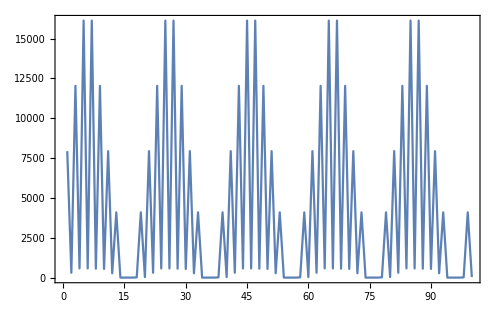

```mathematica
(Table[((2^8)*(#⟦i⟧)+(#⟦i+1⟧)),{i,1,100}]&@(convert/@data))//ListLinePlot
```

```mathematica
rawhexData="['0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0']";
```

```mathematica
formatHex[h_String]:=StringPadLeft[(StringSplit[h,{"'","0x"}]//Last),2,"0"]
```

```mathematica
StringSplit[rawhexData,{"[","]",","}]
```

{'0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0xff', '0x2f', '0xfe', '0x3f', '0xfe', '0x3f', '0xfe', '0x2f', '0xfe', '0x1f', '0xff', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0'}

```mathematica
BaseForm[10,16]
```

a_16

```mathematica
16^^1fff
```

8191

```mathematica
BaseForm["FF"16,10]
```

FF^16

```mathematica
"ff"[[1]]
```

Part::partd: Part specification ff⟦1⟧ is longer than depth of object.

ff⟦1⟧

```mathematica
hextodec[s_String]:=16^^1fff
```

```mathematica
{"1f","ff"}
```

{1f,ff}

```mathematica
?FromDigits
```

```mathematica
FromDigits["ff",16]
```

255

```mathematica
?StringPadLeft
```

```mathematica
StringPadLeft["3",2,"0"]
```

03

```mathematica
formatHex/@StringSplit[rawhexData,{"[","]",","}]
```

{1f,ff,2f,fe,3f,fe,3f,fe,2f,fe,1f,ff,10,00,00,00,00,00,10,00,1f,ff,2f,fe,3f,fe,3f,fe,2f,fe,1f,ff,10,00,00,00,00,00,10,00,1f,ff,2f,fe,3f,fe,3f,fe,2f,fe,1f,ff,10,00,00,00,00,00,10,00,1f,ff,2f,fe,3f,fe,3f,fe,2f,fe,1f,ff,10,00,00,00,00,00,10,00,1f,ff,2f,fe,3f,fe,3f,fe,2f,fe,1f,ff,10,00,00,00,00,00,10,00,1f,ff,2f,fe,3f,fe,3f,fe,2f,fe,1f,ff,10,00,00,00,00,00,10,00,1f,ff,2f,fe,3f,fe,3f,fe,2f,fe,1f,ff,10,00,00,00,00,00,10,00,1f,ff,2f,fe,3f,fe,3f,fe,2f,fe,1f,ff,10,00,00,00,00,00,10,00,1f,ff,2f,fe,3f,fe,3f,fe,2f,fe,1f,ff,10,00,00,00,00,00,10,00,1f,ff,2f,fe,3f,fe,3f,fe,2f,fe,1f,ff,10,00,00,00,00,00,10,00}

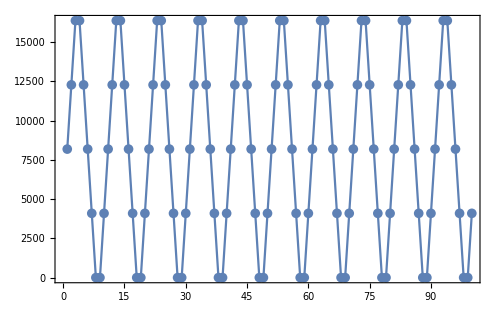

```mathematica
ListLinePlot[(FromDigits[(#1<>#2),16]&@@@Partition[(formatHex/@StringSplit[rawhexData,{"[","]",","}]),2]),Mesh->All]
```

```mathematica
rawData2="['0x23', '0x33', '0x32', '0x30', '0x30', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0']"
```

['0x23', '0x33', '0x32', '0x30', '0x30', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0', '0x0', '0x0', '0x0', '0x10', '0x0', '0x1f', '0x3f', '0x2f', '0x3e', '0x3f', '0x3e', '0x3f', '0x3e', '0x2f', '0x3e', '0x1f', '0x3f', '0x10', '0x0', '0x0']

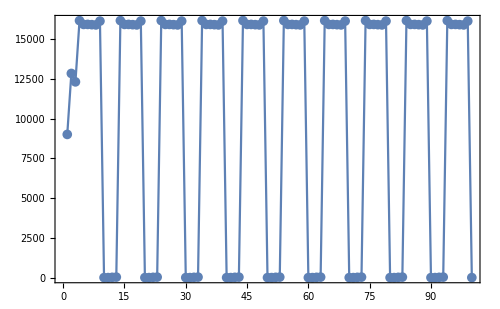

```mathematica
ListLinePlot[(FromDigits[(#1<>#2),16]&@@@Partition[(formatHex/@StringSplit[rawData2,{"[","]",","}]),2]),Mesh->All]
```

```mathematica
"ÿ.1fþ/þ?þ?þ/ÿ.1f"
```